# Configurable photonic simulator for quantum field dynamics

^1Mauro D’Achille, ^1Martin Gärttner, and ^(2,3)Tobias Haas

^1Institute of Condensed Matter Theory and Optics, Friedrich-Schiller-University Jena, Max-Wien-Platz 1, 07743 Jena, Germany
^2Institut für Theoretische Physik and IQST, Universität Ulm, Albert-Einstein-Allee 11, 89069 Ulm, Germany
^3Centre for Quantum Information and Communication, École polytechnique de Bruxelles, CP 165, Université libre de Bruxelles, 1050 Brussels, Belgium

Notebook to the paper that produces Figs. 4, 5, 6, 7 and 10.

The notebook is auto-run

```mathematica
(* Evaluate here to run the notebook. *)
```

Setup

### Plotting

#### Colors

```mathematica
(* Define standard colors for figures (blue, red green) with adjustable opacity. *)
PlotColors[opacity_]:={RGBColor[0,68/255,136/255,opacity],
RGBColor[187/255,85/255,102/255,opacity],
RGBColor[17/255,119/255,51/255,opacity]};

(* Define continuous color gradients. *)
ContinuousColors[start_,end_]:=ColorData[{"BlueGreenYellow",{start,end}}];
```

#### Arrowheads

```mathematica
(* Define nice arrowheads in black, blue, and red. *)
NiceArrowHeadsBlack=Graphics[{Black,Triangle[{{0,0.5},{0,-0.5},{1,0}}]}];
NiceArrowHeadsBlue=Graphics[{PlotColors[1][[1]],Triangle[{{0,0.5},{0,-0.5},{1,0}}]}];
NiceArrowHeadsRed=Graphics[{PlotColors[1][[2]],Triangle[{{0,0.5},{0,-0.5},{1,0}}]}];
```

#### Plotmarkers

```mathematica
(* Define nice plotmarkers for ListPlot[]. *)NicePlotmarkers[size_,edgethickness_,backgroundcolor_,edgecolor_,edgeopacity_,form_]:={Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Opacity[edgeopacity],Thickness[edgethickness]]],Disk[{0,0},1]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Opacity[edgeopacity],Thickness[edgethickness]]],Triangle[{{0,0},{1,0},{1/2,Sqrt[3]/2}}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Opacity[edgeopacity],Thickness[edgethickness]]],Polygon[{{0,0},{1/2,-1/2},{1,0},{1/2,1/2}}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Opacity[edgeopacity],Thickness[edgethickness]]],Rectangle[{-1/2,-1/2},{1/2,1/2}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Opacity[edgeopacity],Thickness[edgethickness]]],Triangle[{{0,0},{1,0},{1/2,-Sqrt[3]/2}}]},ImageSize->size]}[[form]];
```

#### Figs. 4 and 10

```mathematica
(* Plotstyles for Fig. 4. *)
Fig4PlotStyles=Table[{Thickness[0.0065],ContinuousColors[0.8,0][i],Opacity[0.6]},{i,0,0.8,0.2}];
Fig4PlotMarkers=Table[NicePlotmarkers[8,0.33,White,ContinuousColors[0.8,0][i],0.6,i*5+1],{i,0,0.8,0.2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Fig. 5

```mathematica
(* Plotstyles for Fig. 5. *)
Fig5InsetPlotColors=ColorData[{"SandyTerrain",{0,8}}];

(* Function to cut off plot range below the light cone. *)
GenerateWhiteRegion[data_]:=Table[Graphics[{White,Rectangle[{data[[i,1]]-0.5,0},{data[[i,1]]+0.5,data[[i,2]]}]}],{i,1,Length[data]}];
```

#### Fig. 6

```mathematica
(* Plotstyles for Fig. 6. *)
Fig6PlotStyles=Table[{Thickness[0.0065],ContinuousColors[0.8,0][i],Opacity[0.6]},{i,0.,0.8,0.8/3}];
Fig6PlotMarkers={NicePlotmarkers[8,0.33,White,ContinuousColors[0.8,0][0.],0.6,5],
NicePlotmarkers[7,0.5,White,ContinuousColors[0.8,0][0.8/3],0.6,4],
NicePlotmarkers[8,0.33,White,ContinuousColors[0.8,0][2*0.8/3],0.6,2],
NicePlotmarkers[7,0.5,White,ContinuousColors[0.8,0][0.8],0.6,1]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Fig. 7

```mathematica
(* Plotstyles for Fig. 7. *)
Fig7PlotMarkers={NicePlotmarkers[8,1.,White,ContinuousColors[0.8,0][0.],0.8,5],
NicePlotmarkers[7,1.,White,ContinuousColors[0.8,0][0.8/3],0.8,4],
NicePlotmarkers[8,1.,White,ContinuousColors[0.8,0][2*0.8/3],0.8,2],
NicePlotmarkers[7,1.,White,ContinuousColors[0.8,0][0.8],0.8,1]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Saving/Loading

```mathematica
(* Set directory to the notebook directory. *)
SetDirectory[NotebookDirectory[]];
```

### Symplectic metric

```mathematica
(* Define the symplectic form Ω. *)
SymplecticForm[n_]:=KroneckerProduct[I*PauliMatrix[2],IdentityMatrix[n]];
```

### Fractional Hamiltonian

#### Hamiltonian matrix

```mathematica
(* Define the Hamiltonian matrix H for the fractional Laplacian theory: n modes, exponent α, mass m, lattice spacing ϵ. *)
FractionalHamiltonianMatrixϕ[n_,α_,m_,ϵ_]:=Module[{Hϕ,i,j},
Hϕ=ConstantArray[0,{n,n}];
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
Hϕ[[i,j]]=
Sum[(1/ϵ)*Exp[-2*I*Pi*k*(i-j)/n]*((2*Sin[π*k/n])^α)/n,{k,0,n-1}]+ KroneckerDelta[i,j]*ϵ*m^α]];Hϕ]//N;

(* Define the corresponding coupling strength Subscript[f, M]. *)
FractionalCoupling[n_,α_,ϵ_,M_]:=Abs[Sum[(1/ϵ)*Exp[-2*I*π*M*k/n]*((2*Sin[π*k/n])^α)/n,{k,0,n-1}]];
```

#### Relativistic light-cone parameters

```mathematica
(* Maximum quasi-particle velocity. *)
vmax[n_,m_,ϵ_]:=Max[Table[Sin[2π*k/n]/(ϵ*Sqrt[m^2+(4/ϵ^2)*Sin[π*k/n]^2]),{k,0,n-1}]];

(* First appearance of correlations. Divided by n already! *)
τ[n_,M_,m_,ϵ_]:=(M*ϵ)/(2*n*vmax[M,m,ϵ]);
```

### Covariance matrix

#### Generating time evolution

```mathematica
(* The following function generates the time evolution of the covariance matrix by means of the OTA for the fractional Laplacian theory. *)
TimeEvolutionCovarianceMatrix[t_,Δt_,n_,α_,m_,ϵ_]:= Module[
{Hϕ,Hπ,EigenValHϕ, EigenVecHϕ,
GammaNEigenVal,GammaN,
NewEigenVec= {},
TallyFlag, PositionFlag,
OrthogonalZ,BlockTN,
BN, AN,SSD,
InvBN,InvAN,InvSSD,
SymplecticEigenVal,DN,WilliamsonD,
PSTimeEvo,
SSDProduct,
TimeEvolutionCovMat,
CovMatTable,i},

(* Hamiltonian matrix. *)
 Hϕ = FractionalHamiltonianMatrixϕ[n,α,m,ϵ];
 
Hπ = IdentityMatrix[n]/ϵ;

(* Eigenvectors and eigenvalues of Hϕ. *)
{EigenValHϕ, EigenVecHϕ} = Re[Eigensystem[Hϕ]];

(* Diagonal matrix ΓN. *)
GammaNEigenVal=Sqrt[ϵ*EigenValHϕ];
GammaN=DiagonalMatrix[GammaNEigenVal];

(* Symplectic eigenvalues and the corresponding diagonal matrix. *)
SymplecticEigenVal=EigenValHϕ/GammaNEigenVal;
DN=DiagonalMatrix[SymplecticEigenVal];
WilliamsonD=ArrayFlatten[{{DN,0},{0,DN}}] ;

(* Orthogonal set of eigenvectors (in a given subspace with degenerate eigenvalues). *)
TallyFlag = Tally[EigenValHϕ,Abs[#1-#2]<10^(-10)&];
For[i=1, i<=Length[TallyFlag], i++,
PositionFlag=Flatten[Position[EigenValHϕ,_?(Abs[#-TallyFlag[[i]][[1]]]<10^(-10)&)]];
If[TallyFlag[[i]][[2]]==1,
AppendTo[NewEigenVec, EigenVecHϕ[[PositionFlag[[1]]]]],
OrthogonalZ = Orthogonalize[{EigenVecHϕ[[PositionFlag[[1]]]], EigenVecHϕ[[PositionFlag[[2]]]]}, Dot];
AppendTo[NewEigenVec,OrthogonalZ[[1]]];
AppendTo[NewEigenVec, OrthogonalZ[[2]]]]];

(* T given by the polar decomposition. *)
BlockTN = Normalize/@NewEigenVec;

(* Normalize the orthogonal eigenvectors to define BN. *)
BN = Sqrt[GammaNEigenVal]*BlockTN;

(* Define A and SSD matrices. *)
AN = -Inverse[GammaN].BN;
SSD = ArrayFlatten[{{BN,0},{0,-AN}}] ;

(* Invert matrices. *)
InvBN=Transpose[BN].Inverse[GammaN];
InvAN=Transpose[AN].GammaN;
InvSSD=ArrayFlatten[{{InvBN,0},{0,-InvAN}}] ;

(* SSD product appearing in the middle of the time-evolved covariance matrix. *)
SSDProduct=ArrayFlatten[{{GammaN,0},{0,Inverse[GammaN]}}];

(* PS in the middle of the decomposition. *)
PSTimeEvo[tFlag_]:=MatrixExp[tFlag*SymplecticForm[n].WilliamsonD];

(* Time-evolved covariance matrix for vacuum input. *)
TimeEvolutionCovMat[tFlag_]:=Chop[0.5*InvSSD.PSTimeEvo[tFlag].SSDProduct.Transpose[InvSSD.PSTimeEvo[tFlag]]];

CovMatTable=Table[TimeEvolutionCovMat[tInt],{tInt,0,t,Δt}]]
```

#### Selecting subsystems

```mathematica
(* Local covariance matrix corresponding to the first M modes given the full covariance matrix. *)
FirstMMatrix[data_,M_]:=
ArrayFlatten[{{Take[data,{1,M},{1,M}],Take[data,{1,M},{Length[data]/2+1,Length[data]/2+M}]},{Take[data,{Length[data]/2+1,Length[data]/2+M},{1,M}],Take[data,{Length[data]/2+1,Length[data]/2+M},{Length[data]/2+1,Length[data]/2+M}]}}];

(* Local covariance matrix corresponding to the last M modes given the full covariance matrix. *)
LastMMatrix[data_,M_]:=Module[{ModesNumber=Length[data]/2},
ArrayFlatten[{{Take[data,{ModesNumber-M+1,ModesNumber},{ModesNumber-M+1,ModesNumber}],
Take[data,{ModesNumber-M+1,ModesNumber},{2*ModesNumber-M+1,2*ModesNumber}]},
{Take[data,{2*ModesNumber-M+1,2*ModesNumber},{ModesNumber-M+1,ModesNumber}],
Take[data,{2*ModesNumber-M+1,2*ModesNumber},{2*ModesNumber-M+1,2*ModesNumber}]}}]];
```

```mathematica
(* Covariance matrix of two intervals of size M separated by distance d given the full covariance matrix. *)
NonLocalMatrix[data_,M_,d_]:=Module[{BlockAxx, BlockAxp,BlockApp,
BlockBxx,BlockBxp,BlockBpp,
BlockABxx,BlockABpp,BlockABUR,BlockABBL,
CovMatA,CovMatB,
CovMatABxx,CovMatABpp,CovMatABxp,CovMatAB,
CovMatFlag},

(* Local block for A. *)
BlockAxx=data[[1;;M,1;;M]];
BlockAxp=data[[1;;M,Length[data]/2+1;;Length[data]/2+M]];
BlockApp=data[[Length[data]/2+1;;Length[data]/2+M,Length[data]/2+1;;Length[data]/2+M]];
CovMatA=ArrayFlatten[{{BlockAxx,BlockAxp},{Transpose[BlockAxp],BlockApp}}];

(* Local block for B. *)
BlockBxx=data[[M+d+1;;2*M+d,M+d+1;;2*M+d]];
BlockBxp=data[[M+d+1;;2*M+d,Length[data]/2+M+d+1;;Length[data]/2+2*M+d]];
BlockBpp=data[[Length[data]/2+M+d+1;;Length[data]/2+2*M+d,Length[data]/2+M+d+1;;Length[data]/2+2*M+d]];
CovMatB=ArrayFlatten[{{BlockBxx,BlockBxp},{Transpose[BlockBxp],BlockBpp}}];

(* Non-local block for AB. *)
BlockABxx=data[[1;;M,M+d+1;;2*M+d]];
BlockABpp=data[[Length[data]/2+1;;Length[data]/2+M,Length[data]/2+M+d+1;;Length[data]/2+2*M+d]];
BlockABUR=data[[1;;M,Length[data]/2+M+d+1;;Length[data]/2+2*M+d]];
BlockABBL=data[[M+d+1;;2*M+d,Length[data]/2+1;;Length[data]/2+M]];

CovMatABxx=ArrayFlatten[{{BlockAxx,BlockABxx},{Transpose[BlockABxx],BlockBxx}}];
CovMatABpp=ArrayFlatten[{{BlockApp,BlockABpp},{Transpose[BlockABpp],BlockBpp}}];
CovMatABxp=ArrayFlatten[{{BlockAxp,BlockABUR},{BlockABBL,BlockBxp}}];
CovMatAB=ArrayFlatten[{{CovMatABxx,CovMatABxp},{Transpose[CovMatABxp],CovMatABpp}}];

(* Put everything together. *)
CovMatFlag={CovMatA,CovMatB,CovMatAB}];

(* Covariance matrix of two intervals of size M separated by distance d given the full covariance matrix. The first matrix is taken starting from the end. *)
NonLocalMatrixFromEnd[data_,M_,d_]:=Module[{ModesNumber=Length[data]/2,
BlockAxx, BlockAxp,BlockApp,
BlockBxx,BlockBxp,BlockBpp,
BlockABxx,BlockABpp,BlockABUR,BlockABBL,
CovMatA,CovMatB,
CovMatABxx,CovMatABpp,CovMatABxp,CovMatAB,
CovMatFlag},

BlockAxx=data[[ModesNumber-2*M-d+1;;ModesNumber-M-d,ModesNumber-2*M-d+1;;ModesNumber-M-d]];
BlockAxp=data[[ModesNumber-2*M-d+1;;ModesNumber-M-d,2*ModesNumber-2*M-d+1;;2*ModesNumber-M-d]];
BlockApp=data[[2*ModesNumber-2*M-d+1;;2*ModesNumber-M-d,2*ModesNumber-2*M-d+1;;2*ModesNumber-M-d]];
CovMatA=ArrayFlatten[{{BlockAxx,BlockAxp},{Transpose[BlockAxp],BlockApp}}];

BlockBxx=data[[ModesNumber-M+1;;ModesNumber,ModesNumber-M+1;;ModesNumber]];
BlockBxp=data[[ModesNumber-M+1;;ModesNumber,2*ModesNumber-M+1;;2*ModesNumber]];
BlockBpp=data[[2*ModesNumber-M+1;;2*ModesNumber,2*ModesNumber-M+1;;2*ModesNumber]];
CovMatB=ArrayFlatten[{{BlockBxx,BlockBxp},{Transpose[BlockBxp],BlockBpp}}];

(* Let us build the matrix for the union of the regions. *)
BlockABxx=data[[ModesNumber-2*M-d+1;;ModesNumber-M-d,ModesNumber-M+1;;ModesNumber]];
BlockABpp=data[[2*ModesNumber-2*M-d+1;;2*ModesNumber-M-d,2*ModesNumber-M+1;;2*ModesNumber]];
(* Then, we need the Up-Right UR and Bottom-Left BL blocks containg joint information of A and B. *)
BlockABUR=data[[ModesNumber-2*M-d+1;;ModesNumber-M-d,2*ModesNumber-M+1;;2*ModesNumber]];
BlockABBL=data[[ModesNumber-M+1;;ModesNumber,2*ModesNumber-2*M-d+1;;2*ModesNumber-M-d]];

CovMatABxx=ArrayFlatten[{{BlockAxx,BlockABxx},{Transpose[BlockABxx],BlockBxx}}];
CovMatABpp=ArrayFlatten[{{BlockApp,BlockABpp},{Transpose[BlockABpp],BlockBpp}}];
CovMatABxp=ArrayFlatten[{{BlockAxp,BlockABUR},{BlockABBL,BlockBxp}}];
CovMatAB=ArrayFlatten[{{CovMatABxx,CovMatABxp},{Transpose[CovMatABxp],CovMatABpp}}];

CovMatFlag={CovMatA,CovMatB,CovMatAB}]
```

### Entropic measures

#### Photonic simulation

```mathematica
(* Gaussian Rényi-2 entanglement entropy of a given covariance matrix and vacuum input. *)
Renyi2EntanglementEntropyGaussian[data_,M_]:=Module[{CovarianceMatrixInternal=FirstMMatrix[data,M]},
(1/2)*Log[Det[2*CovarianceMatrixInternal]]];

(* Gaussian Rényi-2 mutual information of a given covariance matrix and vacuum input. *)
Renyi2MutualInformationGaussian[data_,M_,d_]:=Module[{CovarianceMatrixA, CovarianceMatrixB,CovarianceMatrixAB,MI},
{CovarianceMatrixA,CovarianceMatrixB,CovarianceMatrixAB}=NonLocalMatrix[data,M,d];
MI=(1/2)*Log[Det[CovarianceMatrixA.CovarianceMatrixB]/Det[CovarianceMatrixAB]]];

(* Gaussian Rényi-2 entanglement entropy of a given covariance matrix and vacuum input, starting from the last modes. *)
Renyi2EntanglementEntropyGaussianFromEnd[data_,M_]:=Module[{CovarianceMatrixInternal=LastMMatrix[data,M]},
(1/2)*Log[Det[2*CovarianceMatrixInternal]]];

(* Gaussian Rényi-2 mutual information of a given covariance matrix and vacuum input, starting from the last modes. *)
Renyi2MutualInformationGaussianFromEnd[data_,M_,d_]:=Module[{CovarianceMatrixA, CovarianceMatrixB,CovarianceMatrixAB,MI},
{CovarianceMatrixA,CovarianceMatrixB,CovarianceMatrixAB}=NonLocalMatrixFromEnd[data,M,d];
MI=(1/2)*Log[Det[CovarianceMatrixA.CovarianceMatrixB]/Det[CovarianceMatrixAB]]];
```

```mathematica
(* The same entropic measures for the photonic simulation with fractional Laplacian theory input parameters. *)
Renyi2EntanglementEntropySimulator[t_,Δt_,n_,M_,α_,m_,ϵ_]:=Module[{data=TimeEvolutionCovarianceMatrix[t,Δt,n,α,m,ϵ]},Table[{Δt*(tInt-1)/n,100*Renyi2EntanglementEntropyGaussian[data[[tInt]],M]/n},{tInt,1,Length[data]}]];

Renyi2MutualInformationSimulator[t_,Δt_,n_,M_,d_,α_,m_,ϵ_]:=Module[{data=TimeEvolutionCovarianceMatrix[t,Δt,n,α,m,ϵ]},Table[{Δt*(tInt-1)/n,100*Renyi2MutualInformationGaussian[data[[tInt]],M,d]/n},{tInt,1,Length[data]}]];
```

```mathematica
(* Rényi-2 mutual information of two modes separated by distance M in spacetime. *)
Renyi2MutualInformationSpacetimeSimulator[tend_,tstep_,totalmodes_,distance_,α_,m_,ϵ_]:=Module[{data=TimeEvolutionCovarianceMatrix[tend,tstep,totalmodes,α,m,ϵ]},Flatten[Table[{d-1,tstep*(tInt-1),Renyi2MutualInformationGaussian[data[[tInt]],1,d]},{tInt,1,Length[data]},{d,1,distance+1}],1]];
```

#### QFT prediction

```mathematica
(* Rényi-2 entanglement entropy of the relativistic theory following the quasi-particle picture. *)
Renyi2EntanglementEntropyQFT[t_,n_,M_,m_,ϵ_]:=Module[
{DispertionRelation, GroupVelocity,NumberQP,GGEDensityEntropy,
Part1,Part2,Part3,Domain,
ToBeSummedEE,
FinalEE},

(* Building block functions. *)
DispertionRelation[k_]:=Sqrt[m^2+4*(Sin[π*k/n]/ϵ)^2];
GroupVelocity[k_]:=Abs[Sin[2*π*k/n]/(ϵ*DispertionRelation[k])];
NumberQP[k_]:=Simplify[(1/(ϵ*DispertionRelation[k])+ (ϵ*DispertionRelation[k])-2)/4];
(* If the number of quasiparticles is zero for some mode, the entanglement is also zero. *)
GGEDensityEntropy[k_]:=If[NumberQP[k]!=0,Simplify[Log[-NumberQP[k]^2+(1+NumberQP[k])^2]],0];

(* Function to be summed. *)
Domain[k_]:=FractionalPart[2*GroupVelocity[k]*t/(n*ϵ)];
Part1[k_]:=GGEDensityEntropy[k]*Domain[k];
Part2[k_]:=(M/n)*GGEDensityEntropy[k];
Part3[k_]:=GGEDensityEntropy[k]*(1-Domain[k]);

ToBeSummedEE[k_]:=Piecewise[{{Part1[k],Domain[k]<M/n},
{Part2[k],M/n<=Domain[k]<1-M/n},
{Part3[k],Domain[k]>=1-M/n}}];
If[EvenQ[n],
(* Even N. *)
FinalEE=Simplify[Sum[ToBeSummedEE[k],{k,-n/2+1,n/2}]],
(* Odd N. *)
FinalEE=Simplify[Sum[ToBeSummedEE[k],{k,-(n-1)/2,(n-1)/2}]]]];
```

```mathematica
(* The same for the Rényi-2 mutual information. *)
Renyi2MutualInformationQFT[t_,n_,M_,d_,m_,ϵ_]:=Module[
{d2,
DispersionRelation, 
GroupVelocity,
NumberQP,GGEDensityEntropy,
Part1,PartA,PartB,PartC,
PartA2,PartB2,PartC2,
DomainV,DomainDA,DomainDB,DomainDC,
ToBeSummedMI,
FinalMI},

(* Building block functions. *)
d2=n-2*M-d;

DispersionRelation[k_]:=Sqrt[m^2+4*(Sin[π*k/n]/ϵ)^2];
GroupVelocity[k_]:=Abs[Sin[2*π*k/n]]/(ϵ*DispersionRelation[k]);
NumberQP[k_]:=Simplify[(1/(ϵ*DispersionRelation[k])+ (ϵ*DispersionRelation[k])-2)/4];
GGEDensityEntropy[k_]:=If[NumberQP[k]!=0,Simplify[Log[-NumberQP[k]^2+(1+NumberQP[k])^2]],0];

(* Functions to be summed. *)
DomainV[k_]:=FractionalPart[GroupVelocity[k]*t/(n*ϵ)];
DomainDA[distance_]:=distance/(2*n);
DomainDB[distance_]:=(distance+2*M)/(2*n);
DomainDC[distance_]:=(distance+M)/(2*n);

Part1[k_]:=DomainV[k]*GGEDensityEntropy[k];

PartA2[k_,distance_]:=DomainDA[distance]*GGEDensityEntropy[k];
PartA[k_,distance_]:=Piecewise[{{Part1[k],DomainV[k]>DomainDA[distance]},{PartA2[k,distance],DomainV[k]<=DomainDA[distance]}}];

PartB2[k_,distance_]:=DomainDB[distance]*GGEDensityEntropy[k];
PartB[k_,distance_]:=Piecewise[{{Part1[k],DomainV[k]>DomainDB[distance]},{PartB2[k,distance],DomainV[k]<=DomainDB[distance]}}];

PartC2[k_,distance_]:=DomainDC[distance]*GGEDensityEntropy[k];
PartC[k_,distance_]:=Piecewise[{{Part1[k],DomainV[k]>DomainDC[distance]},{PartC2[k,distance],DomainV[k]<=DomainDC[distance]}}];

ToBeSummedMI[k_]:=PartA[k,d]+PartB[k,d]-2*PartC[k,d]+PartA[k,d2]+PartB[k,d2]-2*PartC[k,d2]+PartA[k,n+d]+PartB[k,n+d]-2*PartC[k,n+d]+PartA[k,n+d2]+PartB[k,n+d2]-2*PartC[k,n+d2];

(* Notice the extra factor of "2" in the following. *)
If[EvenQ[n],
(* Even N. *)
FinalMI=Simplify[2*Sum[ToBeSummedMI[k],{k,-n/2+1,n/2}]],
(* Odd N. *)
FinalMI=Simplify[2*Sum[ToBeSummedMI[k],{k,-(n-1)/2,(n-1)/2}]]]];
```

### Entropic measures with errors

#### OTA parameters [real DFT case]

```mathematica
(* The following functions are based on Sec. IV A of the manuscript. *)
(* In the following, we compute the symplectic eigenvalues, the parameters for the real squeezers and the interferometer layer, for the fraction Laplacian Hamiltonian. *)
SymplecticEigVal[n_,α_,m_,ϵ_]:=Module[{eps=N[ϵ],lambdaPhi={}, lambdaPi={}, dFlag},
For[i=1, i<=n,i++,
AppendTo[lambdaPhi,Sum[FractionalHamiltonianMatrixϕ[n,α,m,eps][[k,1]]*Cos[2*Pi*(k-1)*(i-1)/n],{k,1,n}]];
AppendTo[lambdaPi,1/eps]];
dFlag=Re[SetPrecision[Sqrt[lambdaPhi*lambdaPi],16]]]

zN[n_,α_,m_,ϵ_]:=Module[{eps=N[ϵ],lambdaPhi={}, lambdaPi={}, dFlag},
For[i=1, i<=n,i++,
AppendTo[lambdaPhi,Sum[FractionalHamiltonianMatrixϕ[n,α,m,eps][[k,1]]*Cos[2*Pi*(k-1)*(i-1)/n],{k,1,n}]];
AppendTo[lambdaPi,1/eps]];
dFlag=-SetPrecision[0.5*Log[Re[Sqrt[lambdaPhi/lambdaPi]]],16]]
```

#### Ideal complex squeezer

```mathematica
(* Input state preparation by means of the result in Sec. III B in the manuscript. Switching to complex squeezers is needed for the error analysis on the state preparation. *)
CSqIntensity[t_,n_,α_,m_,ϵ_]:=Module[{eps=N[ϵ],dNFlag={},zNFlag={},CSqIntensityFlag={}},
dNFlag=SymplecticEigVal[n,α,m,eps];
zNFlag=zN[n,α,m,eps];
CSqIntensityFlag=0.5*ArcCosh[Cos[dNFlag*t]^2+Sin[dNFlag*t]^2*Cosh[4*zNFlag]]]

CSqAngle[t_,n_,α_,m_,ϵ_]:=Module[
{eps=N[ϵ],dNFlag={},zNFlag={},
xFlag={},yFlag={},CSqAngleFlag={}},

dNFlag=SymplecticEigVal[n,α,m,eps];
zNFlag=zN[n,α,m,eps];
If[t==0,
(* Nothing happens if time is zero. *)
CSqAngleFlag=ConstantArray[0.,n],
xFlag=-Sin[dNFlag*t]^2*Sinh[4*zNFlag];
yFlag=-Sin[2*dNFlag*t]*Sinh[2*zNFlag];
CSqAngleFlag = ArcTan[xFlag,yFlag]];
CSqAngleFlag]
```

#### Gaussian distributed errors

```mathematica
(* SqDrift produces NSamples of points with standard deviation σ around the average values defined by the input array. It will be used for errors in the intensity. *)
CSqNoise[averageList_,stdPercentage_,NSamples_]:=Module[{σ={},SqFlag={}},
σ=stdPercentage*averageList;
For[i=1, i<=Length[averageList],i++,
If[averageList[[i]]==0.,
(* When centered around zero, standard variance set equal to zero. *)
AppendTo[SqFlag,RandomVariate[NormalDistribution[averageList[[i]],0.0001],NSamples]],
AppendTo[SqFlag,RandomVariate[NormalDistribution[averageList[[i]],Abs[σ[[i]]]],NSamples]]]];
SqFlag]

(* GlobalSqDrift produces NSamples of points with a costant  standard deviation. It will be used for errors in the angles. *)
CSqNoiseConstantDev[averageList_,stdPercentage_,NSamples_]:=Module[{SqFlag={}},
For[i=1, i<=Length[averageList],i++,
AppendTo[SqFlag,RandomVariate[NormalDistribution[averageList[[i]],Abs[stdPercentage]],NSamples]]];
SqFlag]
```

#### Entropic measures for low frequency errors

```mathematica
(* Entropic measures previously defined with Gaussian distributed errors on the complex squeezer parameters, i.e. input state to the interferometer. ErrorParameter is 0 for no errors, 1 for intensity errors and 2 for angle errors of the input state. *)
EntropicMeasuresLowFreqErrors[t_,timePoints_,n_,α_,m_,ϵ_,M_,d_,ErrorParameter_,stdPercentage_,NSamples_]:=Module[
{eps=N[ϵ],tInt=0.,
dNFlag={},zNFlag={},
xFlag={},yFlag={},
CSqIntensityIdealFlag={},CSqAngleIdealFlag={},
CSqIntensityFlag={},CSqAngleFlag={},
ComplexSqXX={},ComplexSqXP={},ComplexSqPX={},ComplexSqPP={},ComplexSqSquared,
p1={},pCosMatrix,pSinMatrixOrdered,pEven={},
PNFlag,PFlag,
CovMatFlag,
Renyi2Flag={},Renyi2TablePlot={},
MutualInformationFlag={},MITablePlot={}},

(* Interferometer layer (see Sec. IV A in the manuscript). Time-independent, we need to compute it once. *)
pCosMatrix=ConstantArray[0,{n,Ceiling[n/2]-1}];
pSinMatrixOrdered=ConstantArray[0,{n,Ceiling[n/2]-1}];
Clear[i,j];
For[i=1,i<=n,i++,
AppendTo[p1,1/Sqrt[n]];
If[EvenQ[n],AppendTo[pEven,(-1)^(i-1)/Sqrt[n]]];
For[j=2,j<=Ceiling[n/2], j++,
pCosMatrix[[i,j-1]]=Sqrt[2/n]*Cos[2*Pi*(j-1)*(i-1)/n];
pSinMatrixOrdered[[i,-j+1+Ceiling[n/2]]]=Sqrt[2/n]*Sin[2*Pi*(j-1)*(i-1)/n]]];
(* We put everything together for the BS layer. *)
PNFlag=If[OddQ[n],
Join[{p1},Transpose[pCosMatrix],Transpose[pSinMatrixOrdered]],
Join[{p1},Transpose[pCosMatrix],{pEven},Transpose[pSinMatrixOrdered]]];
PFlag=ArrayFlatten[{{PNFlag,0},{0,PNFlag}}];

(* Parameters of interest. *)
dNFlag=SymplecticEigVal[n,α,m,eps];
zNFlag=zN[n,α,m,eps];

(* For here on the time-dependent part. *)
Clear[k]; (* Do not use i and j since the For in ListRenyi2WithErrors contain them. *)
For[k=1,k<=timePoints+1,k++,
xFlag=-Sin[dNFlag*tInt]^2*Sinh[4*zNFlag];
yFlag=-Sin[2*dNFlag*tInt]*Sinh[2*zNFlag];

CSqIntensityIdealFlag=0.5*ArcCosh[Cos[dNFlag*tInt]^2+Sin[dNFlag*tInt]^2*Cosh[4*zNFlag]];
If[tInt==0.,
CSqAngleIdealFlag=ConstantArray[0.,n],
CSqAngleIdealFlag = ArcTan[xFlag,yFlag]];

If[ErrorParameter==0,
(* No errors. *)
CSqIntensityFlag=CSqIntensityIdealFlag;
CSqAngleFlag=CSqAngleIdealFlag;
(* Given the previous lists, we directly compute S.Transpose[S] for the complex squeezer. *)
ComplexSqXX=Cosh[2*CSqIntensityFlag]-Sinh[2*CSqIntensityFlag]*Cos[CSqAngleFlag];
ComplexSqXP=-Sinh[2*CSqIntensityFlag]*Sin[CSqAngleFlag];
ComplexSqPX=-Sinh[2*CSqIntensityFlag]*Sin[CSqAngleFlag];
ComplexSqPP=Cosh[2*CSqIntensityFlag]+Sinh[2*CSqIntensityFlag]*Cos[CSqAngleFlag];
ComplexSqSquared=ArrayFlatten[{{DiagonalMatrix[ComplexSqXX],DiagonalMatrix[ComplexSqXP]},
{DiagonalMatrix[ComplexSqPX],DiagonalMatrix[ComplexSqPP]}}];
(* Let us build CovMat. *)
CovMatFlag=0.5*Transpose[PFlag].ComplexSqSquared.PFlag;
AppendTo[Renyi2Flag,Renyi2EntanglementEntropyGaussian[CovMatFlag,M]];
AppendTo[MutualInformationFlag,Renyi2MutualInformationGaussian[CovMatFlag,M,d]]];

If[ErrorParameter==1,
(* Errors in the intensity. *)
CSqIntensityFlag=Transpose[CSqNoise[CSqIntensityIdealFlag,stdPercentage,NSamples]];
CSqAngleFlag=CSqAngleIdealFlag;
For[i=1,i<=NSamples,i++,
(* Given the previous lists, we directly compute S.Transpose[S] for the complex squeezer. *)
ComplexSqXX=Cosh[2*CSqIntensityFlag[[i]]]-Sinh[2*CSqIntensityFlag[[i]]]*Cos[CSqAngleFlag];
ComplexSqXP=-Sinh[2*CSqIntensityFlag[[i]]]*Sin[CSqAngleFlag];
ComplexSqPX=-Sinh[2*CSqIntensityFlag[[i]]]*Sin[CSqAngleFlag];
ComplexSqPP=Cosh[2*CSqIntensityFlag[[i]]]+Sinh[2*CSqIntensityFlag[[i]]]*Cos[CSqAngleFlag];
(* Let us build CovMat. *)
ComplexSqSquared=ArrayFlatten[{{DiagonalMatrix[ComplexSqXX],DiagonalMatrix[ComplexSqXP]},
{DiagonalMatrix[ComplexSqPX],DiagonalMatrix[ComplexSqPP]}}];
CovMatFlag=0.5*Transpose[PFlag].ComplexSqSquared.PFlag;
AppendTo[Renyi2Flag,Renyi2EntanglementEntropyGaussian[CovMatFlag,M]];
AppendTo[MutualInformationFlag,Renyi2MutualInformationGaussian[CovMatFlag,M,d]]]];

If[ErrorParameter==2,
(* Errors in the angles. *)
CSqIntensityFlag=CSqIntensityIdealFlag;
CSqAngleFlag=Transpose[CSqNoiseConstantDev[CSqAngleIdealFlag,stdPercentage,NSamples]];
For[i=1,i<=NSamples,i++,
(* Given the previous lists, we directly compute S.Transpose[S] for the complex squeezer. *)
ComplexSqXX=Cosh[2*CSqIntensityFlag]-Sinh[2*CSqIntensityFlag]*Cos[CSqAngleFlag[[i]]];
ComplexSqXP=-Sinh[2*CSqIntensityFlag]*Sin[CSqAngleFlag[[i]]];
ComplexSqPX=-Sinh[2*CSqIntensityFlag]*Sin[CSqAngleFlag[[i]]];
ComplexSqPP=Cosh[2*CSqIntensityFlag]+Sinh[2*CSqIntensityFlag]*Cos[CSqAngleFlag[[i]]];
(* Let us build CovMat. *)
ComplexSqSquared=ArrayFlatten[{{DiagonalMatrix[ComplexSqXX],DiagonalMatrix[ComplexSqXP]},
{DiagonalMatrix[ComplexSqPX],DiagonalMatrix[ComplexSqPP]}}];
CovMatFlag=0.5*Transpose[PFlag].ComplexSqSquared.PFlag;
AppendTo[Renyi2Flag,Renyi2EntanglementEntropyGaussian[CovMatFlag,M]];
AppendTo[MutualInformationFlag,Renyi2MutualInformationGaussian[CovMatFlag,M,d]]]];

(* We divide everything by the number of modes and we scale by 100, as we did for the other figures. *)
(* Please, notice that for the low frequency case, the average is at the level of the entropic measures. *)
If[ErrorParameter==0,
AppendTo[Renyi2TablePlot,{tInt/n,100*Renyi2Flag/n}];
AppendTo[MITablePlot,{tInt/n,100*MutualInformationFlag/n}],
AppendTo[Renyi2TablePlot,{tInt/n,100*Mean[Renyi2Flag]/n,100*StandardDeviation[Renyi2Flag]/n}];
AppendTo[MITablePlot,{tInt/n,100*Mean[MutualInformationFlag]/n,100*StandardDeviation[MutualInformationFlag]/n}]];
tInt+=t/timePoints;
Renyi2Flag={};
MutualInformationFlag={}];

Clear[i,j];
{Renyi2TablePlot,MITablePlot}]
```

#### Entropic measures for high frequency errors

```mathematica
(* Entropic measures previously defined with Gaussian distributed errors on the complex squeezer parameters, i.e. input state to the interferometer. ErrorParameter is 0 for no errors, 1 for intensity errors and 2 for angle errors of the input state. *)
(* NEntropySamples controls the number of samples used to compute the standard deviation used for the plot. *)
EntropicMeasuresHighFreqErrors[t_,timePoints_,n_,α_,m_,ϵ_,M_,d_,ErrorParameter_,stdPercentage_,NSamples_,NEntropySamples_]:=Module[
{eps=N[ϵ],tInt=0.,
dNFlag={},zNFlag={},
xFlag={},yFlag={},
CSqIntensityIdealFlag={},CSqAngleIdealFlag={},
CSqIntensityFlag={},CSqAngleFlag={},
ComplexSqXX={},ComplexSqXP={},ComplexSqPX={},ComplexSqPP={},ComplexSqSquared,
p1={},pCosMatrix,pSinMatrixOrdered,pEven={},
PNFlag,PFlag,
CovMatSamples={},MeanCovMat,
Renyi2Flag={},Renyi2TablePlot={},
MutualInformationFlag={},MITablePlot={}},

(* Interferometer layer (see Sec. IV A in the manuscript). Time-independent, we need to compute it once. *)
pCosMatrix=ConstantArray[0,{n,Ceiling[n/2]-1}];
pSinMatrixOrdered=ConstantArray[0,{n,Ceiling[n/2]-1}];
Clear[i,j];
For[i=1,i<=n,i++,
AppendTo[p1,1/Sqrt[n]];
If[EvenQ[n],AppendTo[pEven,(-1)^(i-1)/Sqrt[n]]];
For[j=2,j<=Ceiling[n/2], j++,
pCosMatrix[[i,j-1]]=Sqrt[2/n]*Cos[2*Pi*(j-1)*(i-1)/n];
pSinMatrixOrdered[[i,-j+1+Ceiling[n/2]]]=Sqrt[2/n]*Sin[2*Pi*(j-1)*(i-1)/n]]];
(* We put everything together for the BS layer. *)
PNFlag=If[OddQ[n],
Join[{p1},Transpose[pCosMatrix],Transpose[pSinMatrixOrdered]],
Join[{p1},Transpose[pCosMatrix],{pEven},Transpose[pSinMatrixOrdered]]];
PFlag=ArrayFlatten[{{PNFlag,0},{0,PNFlag}}];

(* Parameters of interest. *)
dNFlag=SymplecticEigVal[n,α,m,eps];
zNFlag=zN[n,α,m,eps];

(* For here on the time-dependent part. *)
Clear[k,l]; (* Do not use i and j since the For in ListRenyi2WithErrors contain them. *)
For[k=1,k<=timePoints+1,k++,
For[l=1,l<=NEntropySamples,l++,
xFlag=-Sin[dNFlag*tInt]^2*Sinh[4*zNFlag];
yFlag=-Sin[2*dNFlag*tInt]*Sinh[2*zNFlag];

CSqIntensityIdealFlag=0.5*ArcCosh[Cos[dNFlag*tInt]^2+Sin[dNFlag*tInt]^2*Cosh[4*zNFlag]];
If[tInt==0.,
CSqAngleIdealFlag=ConstantArray[0.,n],
CSqAngleIdealFlag = ArcTan[xFlag,yFlag]];

If[ErrorParameter==0,
(* No errors. *)
CSqIntensityFlag=CSqIntensityIdealFlag;
CSqAngleFlag=CSqAngleIdealFlag;
(* Given the previous lists, we directly compute S.Transpose[S] for the complex squeezer. *)
ComplexSqXX=Cosh[2*CSqIntensityFlag]-Sinh[2*CSqIntensityFlag]*Cos[CSqAngleFlag];
ComplexSqXP=-Sinh[2*CSqIntensityFlag]*Sin[CSqAngleFlag];
ComplexSqPX=-Sinh[2*CSqIntensityFlag]*Sin[CSqAngleFlag];
ComplexSqPP=Cosh[2*CSqIntensityFlag]+Sinh[2*CSqIntensityFlag]*Cos[CSqAngleFlag];
ComplexSqSquared=ArrayFlatten[{{DiagonalMatrix[ComplexSqXX],DiagonalMatrix[ComplexSqXP]},
{DiagonalMatrix[ComplexSqPX],DiagonalMatrix[ComplexSqPP]}}];
(* Let us build CovMat. *)
AppendTo[CovMatSamples,0.5*Transpose[PFlag].ComplexSqSquared.PFlag]];

If[ErrorParameter==1,
(* Errors in the intensity. *)
CSqIntensityFlag=Transpose[CSqNoise[CSqIntensityIdealFlag,stdPercentage,NSamples]];
CSqAngleFlag=CSqAngleIdealFlag;
For[i=1,i<=NSamples,i++,
(* Given the previous lists, we directly compute S.Transpose[S] for the complex squeezer. *)
ComplexSqXX=Cosh[2*CSqIntensityFlag[[i]]]-Sinh[2*CSqIntensityFlag[[i]]]*Cos[CSqAngleFlag];
ComplexSqXP=-Sinh[2*CSqIntensityFlag[[i]]]*Sin[CSqAngleFlag];
ComplexSqPX=-Sinh[2*CSqIntensityFlag[[i]]]*Sin[CSqAngleFlag];
ComplexSqPP=Cosh[2*CSqIntensityFlag[[i]]]+Sinh[2*CSqIntensityFlag[[i]]]*Cos[CSqAngleFlag];
(* Let us build CovMat. *)
ComplexSqSquared=ArrayFlatten[{{DiagonalMatrix[ComplexSqXX],DiagonalMatrix[ComplexSqXP]},
{DiagonalMatrix[ComplexSqPX],DiagonalMatrix[ComplexSqPP]}}];
AppendTo[CovMatSamples,0.5*Transpose[PFlag].ComplexSqSquared.PFlag]]];

If[ErrorParameter==2,
(* Errors in the angles. *)
CSqIntensityFlag=CSqIntensityIdealFlag;
CSqAngleFlag=Transpose[CSqNoiseConstantDev[CSqAngleIdealFlag,stdPercentage,NSamples]];
For[i=1,i<=NSamples,i++,
(* Given the previous lists, we directly compute S.Transpose[S] for the complex squeezer. *)
ComplexSqXX=Cosh[2*CSqIntensityFlag]-Sinh[2*CSqIntensityFlag]*Cos[CSqAngleFlag[[i]]];
ComplexSqXP=-Sinh[2*CSqIntensityFlag]*Sin[CSqAngleFlag[[i]]];
ComplexSqPX=-Sinh[2*CSqIntensityFlag]*Sin[CSqAngleFlag[[i]]];
ComplexSqPP=Cosh[2*CSqIntensityFlag]+Sinh[2*CSqIntensityFlag]*Cos[CSqAngleFlag[[i]]];
(* Let us build CovMat. *)
ComplexSqSquared=ArrayFlatten[{{DiagonalMatrix[ComplexSqXX],DiagonalMatrix[ComplexSqXP]},
{DiagonalMatrix[ComplexSqPX],DiagonalMatrix[ComplexSqPP]}}];
AppendTo[CovMatSamples,0.5*Transpose[PFlag].ComplexSqSquared.PFlag]]];

(* Please, notice that for the high frequency case, the average is at the level of the covariance matrix. *)
MeanCovMat=Mean[CovMatSamples];
AppendTo[Renyi2Flag,Renyi2EntanglementEntropyGaussian[MeanCovMat,M]];
AppendTo[MutualInformationFlag,Renyi2MutualInformationGaussian[MeanCovMat,M,d]];
CovMatSamples={}];

(* We divide everything by the number of modes and we scale by 100, as we did for the other figures. The second average is used to compute the standard deviation. The central value used for the plot is simply given by one of the entropic measures (not their average), in this case the first one. *)
If[ErrorParameter==0,
AppendTo[Renyi2TablePlot,{tInt/n,100*Renyi2Flag/n}];
AppendTo[MITablePlot,{tInt/n,100*MutualInformationFlag/n}],
AppendTo[Renyi2TablePlot,{tInt/n,100*Renyi2Flag[[1]]/n,100*StandardDeviation[Renyi2Flag]/n}];
AppendTo[MITablePlot,{tInt/n,100*MutualInformationFlag[[1]]/n,100*StandardDeviation[MutualInformationFlag]/n}]];
tInt+=t/timePoints;
Renyi2Flag={};
MutualInformationFlag={}];

Clear[i,j];
{Renyi2TablePlot,MITablePlot}]
```

Fig. 4

### Data generation

#### Photonic simulator

```mathematica
(* Data points for the simulator. *)
Renyi2EntanglementEntropySimulatorData=Table[Renyi2EntanglementEntropySimulator[100,n/5,n,n/5,2,1,2.0],{n,5,25,5}];

Renyi2MutualInformationSimulatorData=Table[Renyi2MutualInformationSimulator[100,n/5,n,n/5,n/5,2,1,2.0],{n,5,25,5}];
```

#### QFT prediction

```mathematica
(* QFT predictions. *)
Renyi2EntanglementEntropyQFTCurve[t_]:=100*Renyi2EntanglementEntropyQFT[t*200,200,40,1,2.0]/200;

Renyi2MutualInformationQFTCurve[t_]:=100*Renyi2MutualInformationQFT[t*200,200,40,40,1,2.0]/200;
```

### Individual plots

#### (a) Renyi-2 entanglement entropy

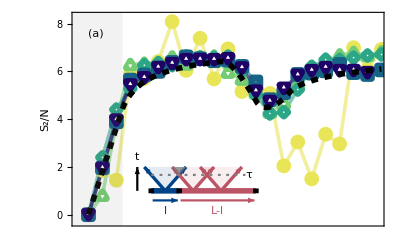

```mathematica
(* Plot the time evolution of the Renyi-2 entanglement entropy for various system sizes against the QFT prediction. *)
Fig4a=Show[ListLinePlot[Renyi2EntanglementEntropySimulatorData,PlotRange->{{-0.15,4.15},{-0.3,8.3}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->Fig4PlotStyles,FrameLabel->{None,Style["S_2/N",Black,FontSize->15]},FrameTicks->{{{0,2,4,6,8},None},{None,None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],ListPlot[Renyi2EntanglementEntropySimulatorData,PlotMarkers->Fig4PlotMarkers],Plot[Renyi2EntanglementEntropyQFTCurve[t],{t,0,4.2},PlotStyle->{{Black,Thickness[0.01],Dashed}},PlotRange->All],Graphics[{Black,FontSize->15,Style[Text["(a)",{0.1,7.6}],Bold],Gray,Opacity[0.1],Rectangle[{-1,-1},{τ[25,5,1,2],9}]}],Graphics[{FontSize->15,Thickness[0.01],PlotColors[1][[1]],Line[{{0.9,1},{1.3,1}}],Thickness[0.006],Arrowheads[{{0.018,0.5,NiceArrowHeadsBlue}}],Arrow[{{1.1,1},{0.8,2}}],Arrow[{{1.1,1},{1.4,2}}],PlotColors[1][[2]],Thickness[0.01],Line[{{1.3,1},{2.4,1}}],Thickness[0.006],Arrowheads[{{0.018,0.5,NiceArrowHeadsRed}}],
Arrow[{{1.5,1},{1.2,2}}],Arrow[{{1.5,1},{1.8,2}}],Arrow[{{1.9,1},{1.6,2}}],Arrow[{{1.9,1},{2.2,2}}],
PlotColors[0.1][[2]],Triangle[{{1.5,1},{1.2,2},{1.8,2}}],Triangle[{{1.9,1},{2.2,2},{1.6,2}}],PlotColors[0.1][[1]],Triangle[{{1.1,1},{0.8,2},{1.4,2}}],Opacity[1],Thickness[0.01],Black,Line[{{0.9,0.9},{0.9,1.1}}],Line[{{1.3,0.9},{1.3,1.1}}],Line[{{2.4,0.9},{2.4,1.1}}],Gray,Opacity[0.7],Triangle[{{1.3,1.6667},{1.4,2},{1.2,2}}],Dashing[{0.005,0.01}],Opacity[1],Thickness[0.004],Line[{{0.9,1.6667},{2.25,1.6667}}],Dashing[None],Black,Thickness[0.004],Arrowheads[{{0.015,0.9,NiceArrowHeadsBlack}}],Arrow[{{0.7,1},{0.7,2}}],FontSize->13,Text["t",{0.7,2.4}],Text["τ",{2.3,1.6667}],PlotColors[1][[1]],Arrowheads[{{-0.015,0.04,NiceArrowHeadsBlue},{0.015,0.96,NiceArrowHeadsBlue}}],Arrow[{{0.92,0.6},{1.28,0.6}}],PlotColors[1][[2]],Arrowheads[{{-0.015,0.04,NiceArrowHeadsRed},{0.015,0.96,NiceArrowHeadsRed}}],Arrow[{{1.32,0.6},{2.38,0.6}}],PlotColors[1][[1]],Text["l",{1.1,0.15}],PlotColors[1][[2]],Text["L-l",{1.85,0.15}]}],ImageSize->{Automatic,180.3}]
```

#### (b) Renyi-2 mutual information

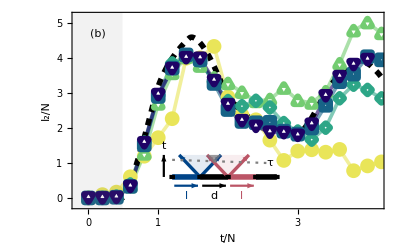

```mathematica
(* Plot the time evolution of the Renyi-2 mutual information for various system sizes against the QFT prediction. *)
Fig4b=Show[ListLinePlot[Renyi2MutualInformationSimulatorData,PlotRange->{{-0.15,4.15},{-0.2,5.2}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->Fig4PlotStyles,FrameLabel->{Style["t/N",Black,FontSize->15],Style["I_2/N",Black,FontSize->15]},FrameTicks->{{{0,1,2,3,4,5},None},{{0,{τ[25,5,1,2],"τ/N"},1,2,3,4},None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],
Plot[Renyi2MutualInformationQFTCurve[t],{t,0,4.2},PlotStyle->{{Black,Thickness[0.01],Dashed}},PlotRange->All],ListPlot[Renyi2MutualInformationSimulatorData,PlotMarkers->Fig4PlotMarkers],Graphics[{Black,FontSize->15,Style[Text["(b)",{0.13,4.7}],Bold],Gray,Opacity[0.1],Rectangle[{-1,-1},{τ[25,5,1,2],9}]}],Graphics[{FontSize->15,Thickness[0.01],PlotColors[1][[1]],Line[{{1.2,0.6},{1.6,0.6}}],Thickness[0.006],Arrowheads[{{0.018,0.5,NiceArrowHeadsBlue}}],Arrow[{{1.6,0.6},{1.3,1.23}}],Arrow[{{1.6,0.6},{1.9,1.23}}],Black,Thickness[0.01],Line[{{1.6,0.6},{2,0.6}}],Line[{{2.4,0.6},{2.7,0.6}}],PlotColors[1][[2]],Line[{{2,0.6},{2.4,0.6}}],Thickness[0.006],Arrowheads[{{0.018,0.5,NiceArrowHeadsRed}}],
Arrow[{{2,0.6},{1.7,1.23}}],Arrow[{{2,0.6},{2.3,1.23}}],
PlotColors[0.1][[2]],Triangle[{{2,0.6},{1.7,1.23},{2.3,1.23}}],PlotColors[0.1][[1]],Triangle[{{1.6,0.6},{1.3,1.23},{1.9,1.23}}],Opacity[1],Thickness[0.01],Black,Line[{{1.2,0.54},{1.2,0.66}}],Line[{{1.6,0.54},{1.6,0.66}}],Line[{{2.4,0.54},{2.4,0.66}}],Line[{{2,0.54},{2,0.66}}],Line[{{2.7,0.54},{2.7,0.66}}],FontSize->13,Gray,Opacity[0.7],Triangle[{{1.8,1},{1.9,1.23},{1.7,1.23}}],Dashing[{0.005,0.01}],Opacity[1],Thickness[0.004],Line[{{1.2,1.09},{2.55,1}}],Dashing[None],Black,Thickness[0.004],Arrowheads[{{0.015,0.9,NiceArrowHeadsBlack}}],Arrow[{{1.08,0.6},{1.08,1.23}}],Text["t",{1.08,1.48}],Text["τ",{2.6,1}],PlotColors[1][[1]],Arrowheads[{{-0.015,0.04,NiceArrowHeadsBlue},{0.015,0.96,NiceArrowHeadsBlue}}],Arrow[{{1.23,0.35},{1.57,0.35}}],PlotColors[1][[2]],Arrowheads[{{-0.015,0.04,NiceArrowHeadsRed},{0.015,0.96,NiceArrowHeadsRed}}],Arrow[{{2.03,0.35},{2.37,0.35}}],Black,Arrowheads[{{-0.015,0.04,NiceArrowHeadsBlack},{0.015,0.96,NiceArrowHeadsBlack}}],Arrow[{{1.63,0.35},{1.97,0.35}}],Text["d",{1.8,0.065}],PlotColors[1][[1]],Text["l",{1.4,0.065}],PlotColors[1][[2]],Text["l",{2.2,0.065}]}],ImageSize->{Automatic,220}]
```

### Final figure

```mathematica
(* Combine the latter two plots with a bar legend. *)
Fig4=Legended[Grid[{{Rasterize[Fig4a,ImageResolution->300,ImageSize->{Automatic,181}],,,,,,,,,,,,},{Rasterize[Fig4b,ImageResolution->300,ImageSize->{Automatic,220}]}},Alignment->Left,Spacings->{0,0}],Placed[Rasterize[BarLegend[{ContinuousColors[0.8,0],{0,0.8}},LabelStyle->{Black,FontSize->12},LegendMarkerSize->160,Ticks->{{0,"5"},{0.2,"10"},{0.4,"15"},{0.6,"20"},{0.8,"25"}},LegendLabel->Style["N",FontSize->14,Black]],ImageResolution->300],{1,0.607}]]
```

-Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
(* To export the pdf. *)
(* Export[FileNameJoin[{"EntanglementGeneration.pdf"}],Fig4,ImageResolution->Automatic,"AllowRasterization"->True] *)
```

EntanglementGeneration.pdf

```mathematica
(* Compute τ/N. *)
τ[25,5,1,2]//N
```

0.487859

Fig. 5

### Data generation

#### Photonic simulator

```mathematica
(* Generate data sets. *)

(* α=2 (relativistic). *)
RenyiMISimulatorRelativisticData=Renyi2MutualInformationSpacetimeSimulator[0.5,0.01,20,6,2,1,0.1];

(* α=1.5. *)
RenyiMISimulatorFractionalα15Data=Renyi2MutualInformationSpacetimeSimulator[0.5,0.01,20,6,1.5,1,0.1];

(* α=1. *)
RenyiMISimulatorFractionalα1Data=Renyi2MutualInformationSpacetimeSimulator[0.5,0.01,20,6,1,1,0.1];

(* α=0.5. *)
RenyiMISimulatorFractionalα05Data=Renyi2MutualInformationSpacetimeSimulator[0.5,0.01,20,6,0.5,1,0.1];

(* α->0. *)
RenyiMISimulatorFractionalα0Data=Renyi2MutualInformationSpacetimeSimulator[0.5,0.01,20,6,0.0001,1,0.1];
```

#### Light cones

```mathematica
(* Function that selects the points of the informational wave front. *)
FitPoints[data_,modes_,threshold_]:=Module[{data2=Transpose[Partition[data,modes]]},Module[{data3=Table[SelectFirst[data2[[j]],#[[3]]>=threshold&],{j,1,Length[data2]}]},Table[{data3[[k,1]],data3[[k,2]]},{k,1,Length[data3]}]]];
```

```mathematica
(* Points to be fit. *)

(* α=2 (relativistic). *)
RenyiMISimulatorRelativisticFitPoints=FitPoints[RenyiMISimulatorRelativisticData,7,0.01];

(* α=1.5. *)
RenyiMISimulatorFractionalα15FitPoints=FitPoints[RenyiMISimulatorFractionalα15Data,7,0.01];

(* α=1. *)
RenyiMISimulatorFractionalα1FitPoints=FitPoints[RenyiMISimulatorFractionalα1Data,7,0.01];

(* α=0.5. *)
RenyiMISimulatorFractionalα05FitPoints=FitPoints[RenyiMISimulatorFractionalα05Data,7,0.01];

(* α->0. *)
RenyiMISimulatorFractionalα0FitPoints=FitPoints[RenyiMISimulatorFractionalα0Data,7,0.01];
```

#### Fits

```mathematica
(* Fit functions up to modes. *)

(* Linear. *)
ComputeLinearFit[data_,modes_]:=NonlinearModelFit[Take[data,modes],a*x+b,{a,b},x]//Normal;

(* Algebraic. *)
ComputeAlgebraicFit[data_,modes_]:=NonlinearModelFit[Take[data,modes],{c+b*(x)^a,{0.1<a<0.9,d>0}},{a,b,c,d},x,Method->"NMinimize",MaxIterations->1000]//Normal;

(* Logarithmic. *)
ComputeLogarithmicFit[data_,modes_]:=NonlinearModelFit[Take[data,modes],{a+b*Log[x+c],{b>0,c>0}},{a,b,c},x,Method->"NMinimize",MaxIterations->1000]//Normal;
```

```mathematica
(* Compute fits. *)

(* α=2 (relativistic). *)
RenyiMISimulatorRelativisticFit=ComputeLinearFit[RenyiMISimulatorRelativisticFitPoints,7]

(* α=1.5. *)
RenyiMISimulatorFractionalα15Fit=ComputeAlgebraicFit[RenyiMISimulatorFractionalα15FitPoints,7]

(* α=1. *)
RenyiMISimulatorFractionalα1Fit=ComputeAlgebraicFit[RenyiMISimulatorFractionalα1FitPoints,7]

(* α=0.5. *)
RenyiMISimulatorFractionalα05Fit=ComputeLogarithmicFit[RenyiMISimulatorFractionalα05FitPoints,7]

(* α->0. *)
RenyiMISimulatorFractionalα0Fit=ComputeLinearFit[RenyiMISimulatorFractionalα0FitPoints,7]
```

0.0546429+0.0632143 x

0.0706742+0.0675722 x^0.774829

0.088067+0.0650877 x^0.531365

0.138783+0.0349807 Log[0.43598+x]

0.16+3.44249×10^-18 x

### Individual plots

#### (a) inset: decay of interactions

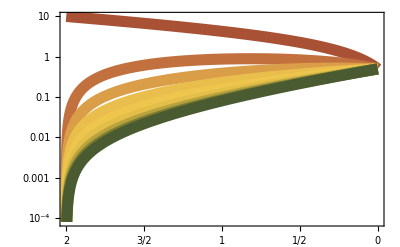

```mathematica
(* Plot of the coupling strength as a function of α for various M. *)
Fig5aInset=Show[Table[LogPlot[FractionalCoupling[20,α,0.1,j],{α,2,0},ScalingFunctions->{"Reverse",Identity},PlotTheme->"Detailed",PlotRange->{{-0.2,2.2},{0.00008,30}},PlotLegends->None,PlotStyle->{Thickness[0.02],Fig5InsetPlotColors[j-1]},FrameLabel->None,FrameTicks->{{None,{{0.0001,"10^-4"},{0.01,"10^-2"},1}},{{0,{1/2,"1/2"},1,{3/2,"3/2"},2},None}},FrameStyle->Directive[Black,Thickness[0.013]],FrameTicksStyle->Directive[Black,FontSize->9.5],GridLines->None],{j,1,9,1}],ImageSize->{Automatic,65}]
```

#### (a): Overview

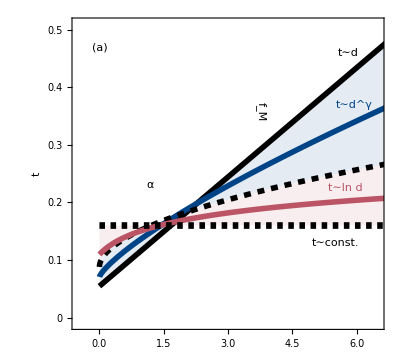

```mathematica
(* Plot the Renyi-2 mutual information in spacetime for given α. *)
Fig5a=Legended[Show[Plot[{RenyiMISimulatorRelativisticFit,RenyiMISimulatorFractionalα15Fit,RenyiMISimulatorFractionalα1Fit,RenyiMISimulatorFractionalα05Fit,RenyiMISimulatorFractionalα0Fit},{x,0,7},PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{-0.01,0.51}},PlotLegends->None,PlotStyle->{{Thickness[0.01],Black},{Thickness[0.01],PlotColors[1][[1]]},{Thickness[0.01],Black,Dashed},{Thickness[0.01],PlotColors[1][[2]]},{Thickness[0.012],Black,Dashing[{0.01,0.01}]}},Filling->{1->{{3},Directive[PlotColors[0.1][[1]]]},3->{{5},Directive[PlotColors[0.1][[2]]]}},FrameLabel->{None,Style["t",Black,FontSize->15]},FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},None},{None,None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None,Epilog->Inset[Fig5aInset,{1.6,0.34}]],Graphics[{Black,FontSize->11,Text["α",{1.18,0.231}],Text["f_M",{3.77,0.358},Automatic,{0,-1}],FontSize->12,Text["t∼d",{5.8,0.46},Automatic,{0.5,0.43}],Text["t∼const.",{5.5,0.129}],PlotColors[1][[1]],Text["t∼d^γ",{5.95,0.37},Automatic,{0.5,0.25}],PlotColors[1][[2]],Text["t∼ln d",{5.74,0.225},Automatic,{0.5,0.05}],Black,FontSize->14,Style[Text["(a)",{0,0.47}],Bold]}],AspectRatio->0.9,ImageSize->{Automatic,190}],Placed[BarLegend[{Fig5InsetPlotColors,{0,8}},LabelStyle->{Black,FontSize->7},LegendLayout->"Row",LegendMarkerSize->{70,10},Ticks->{0,2,4,6,8},LegendLabel->Placed[Style["M",FontSize->8,Black],Right]],{0.290,0.93}]]
```

#### (b): α=2

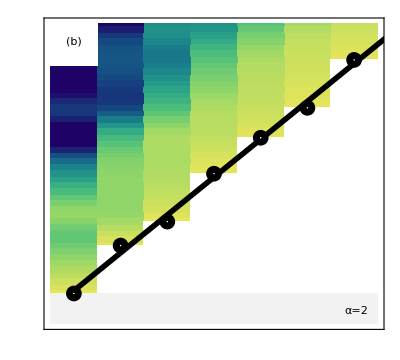

```mathematica
(* α=2 (relativistic). *)
Fig5b=Show[ListDensityPlot[RenyiMISimulatorRelativisticData,PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{0,0.5}},PlotLegends->None,ColorFunction->ContinuousColors[0.2,0.01],ColorFunctionScaling->False,InterpolationOrder->0,FrameLabel->None,FrameTicks->None,FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],GenerateWhiteRegion[RenyiMISimulatorRelativisticFitPoints],Graphics[{Gray,Opacity[0.1],Rectangle[{-0.5,0},{6.5,RenyiMISimulatorRelativisticFitPoints[[1,2]]}],Opacity[1],White,Rectangle[{-0.5,0.43},{0.5,0.55}],Black,FontSize->14,Style[Text["(b)",{0,0.47}],Bold],FontSize->12,Text["α=2",{6.05,0.02}]}],Plot[RenyiMISimulatorRelativisticFit,{x,0,7},PlotStyle->{Black,Thickness[0.01]}],ListPlot[RenyiMISimulatorRelativisticFitPoints,PlotMarkers->NicePlotmarkers[9,0.3,White,Black,1,1]],AspectRatio->0.9,ImageSize->{Automatic,183}]
```

#### (c): α=1.5

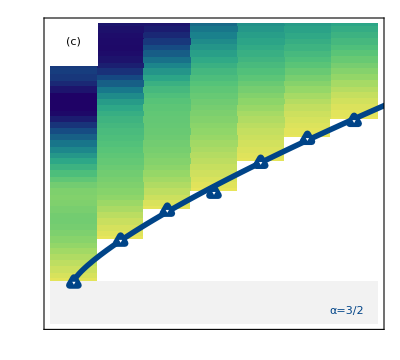

```mathematica
(* α=1.5 *)
Fig5c=Show[ListDensityPlot[RenyiMISimulatorFractionalα15Data,PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{0,0.5}},PlotLegends->None,ColorFunction->ContinuousColors[0.2,0.01],ColorFunctionScaling->False,InterpolationOrder->0,FrameLabel->None,FrameTicks->None,FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],GenerateWhiteRegion[RenyiMISimulatorFractionalα15FitPoints],Graphics[{Gray,Opacity[0.1],Rectangle[{-0.5,0},{6.5,RenyiMISimulatorFractionalα15FitPoints[[1,2]]}],Opacity[1],White,Rectangle[{-0.5,0.43},{0.5,0.55}],Black,FontSize->14,Style[Text["(c)",{0,0.47}],Bold],PlotColors[1][[1]],FontSize->12,Text["α=3/2",{5.85,0.02}]}],Plot[RenyiMISimulatorFractionalα15Fit,{x,0,7},PlotStyle->{PlotColors[1][[1]],Thickness[0.01]}],ListPlot[RenyiMISimulatorFractionalα15FitPoints,PlotMarkers->NicePlotmarkers[9,0.3,White,PlotColors[1][[1]],1,2]],AspectRatio->0.9,ImageSize->{Automatic,183}]
```

#### (d): α=1

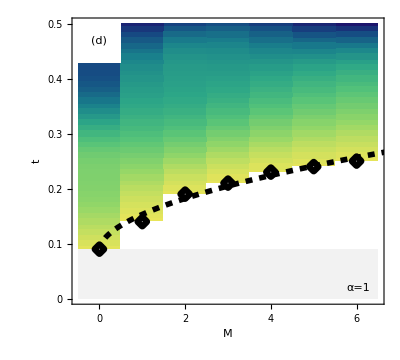

```mathematica
(* α=1. *)
Fig5d=Show[ListDensityPlot[RenyiMISimulatorFractionalα1Data,PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{0,0.5}},PlotLegends->None,ColorFunction->ContinuousColors[0.2,0.01],ColorFunctionScaling->False,InterpolationOrder->0,FrameLabel->{Style["M",Black,FontSize->15],Style["t",Black,FontSize->15]},FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},None},{{0,1,2,3,4,5,6},None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],GenerateWhiteRegion[RenyiMISimulatorFractionalα1FitPoints],Graphics[{Gray,Opacity[0.1],Rectangle[{-0.5,0},{6.5,RenyiMISimulatorFractionalα1FitPoints[[1,2]]}],Opacity[1],White,Rectangle[{-0.5,0.43},{0.5,0.55}],Black,FontSize->14,Style[Text["(d)",{0,0.47}],Bold],FontSize->12,Text["α=1",{6.05,0.02}]}],Plot[RenyiMISimulatorFractionalα1Fit,{x,0,7},PlotStyle->{Black,Thickness[0.01],Dashed}],ListPlot[RenyiMISimulatorFractionalα1FitPoints,PlotMarkers->NicePlotmarkers[9,0.3,White,Black,1,3]],AspectRatio->0.9,ImageSize->{Automatic,227}]
```

#### (e): α=0.5

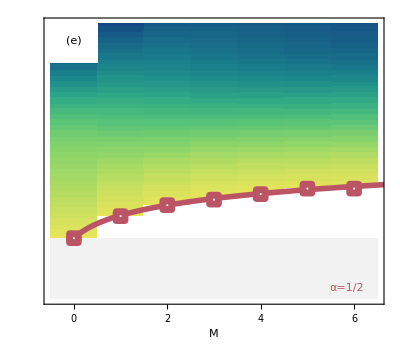

```mathematica
(* α=0.5. *)
Fig5e=Show[ListDensityPlot[RenyiMISimulatorFractionalα05Data,PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{0,0.5}},PlotLegends->None,ColorFunction->ContinuousColors[0.2,0.01],ColorFunctionScaling->False,InterpolationOrder->0,FrameLabel->{Style["M",Black,FontSize->15]},FrameTicks->{{None,None},{{0,1,2,3,4,5,6},None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],GenerateWhiteRegion[RenyiMISimulatorFractionalα05FitPoints],Graphics[{Gray,Opacity[0.1],Rectangle[{-0.5,0},{6.5,RenyiMISimulatorFractionalα05FitPoints[[1,2]]}],Opacity[1],White,Rectangle[{-0.5,0.43},{0.5,0.55}],Black,FontSize->14,Style[Text["(e)",{0,0.47}],Bold],PlotColors[1][[2]],FontSize->12,Text["α=1/2",{5.85,0.02}]}],Plot[RenyiMISimulatorFractionalα05Fit,{x,0,7},PlotStyle->{Thickness[0.01],PlotColors[1][[2]]}],ListPlot[RenyiMISimulatorFractionalα05FitPoints,PlotMarkers->NicePlotmarkers[9,0.3,White,PlotColors[1][[2]],1,4]],AspectRatio->0.9,ImageSize->{Automatic,223.8}]
```

#### (f): α→0

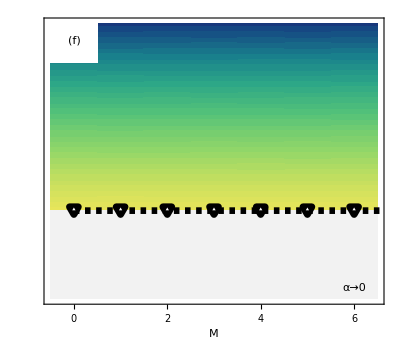

```mathematica
(* α->0. *)
Fig5f=Show[ListDensityPlot[RenyiMISimulatorFractionalα0Data,PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{0,0.5}},PlotLegends->None,ColorFunction->ContinuousColors[0.2,0.01],ColorFunctionScaling->False,InterpolationOrder->0,FrameLabel->{Style["M",Black,FontSize->15]},FrameTicks->{{None,None},{{0,1,2,3,4,5,6},None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],GenerateWhiteRegion[RenyiMISimulatorFractionalα0FitPoints],Graphics[{Gray,Opacity[0.1],Rectangle[{-0.5,0},{6.5,RenyiMISimulatorFractionalα0FitPoints[[1,2]]}],Opacity[1],White,Rectangle[{-0.5,0.43},{0.5,0.55}],Black,FontSize->14,Style[Text["(f)",{0,0.47}],Bold],FontSize->12,Text["α→0",{6,0.02}]}],Plot[RenyiMISimulatorFractionalα0Fit,{x,0,7},PlotStyle->{Black,Thickness[0.012],Dashing[{0.01,0.01}]}],ListPlot[RenyiMISimulatorFractionalα0FitPoints,PlotMarkers->NicePlotmarkers[9,0.3,White,Black,1,5]],AspectRatio->0.9,ImageSize->{Automatic,223.8}]
```

### Final figure

```mathematica
(* Combine the latter six figures. *)
Fig5=Legended[Grid[{{Grid[{{Rasterize[Fig5a,ImageResolution->300,ImageSize->{Automatic,190}],
Rasterize[Fig5b,ImageResolution->300,ImageSize->{Automatic,183}],
Rasterize[Fig5c,ImageResolution->300,ImageSize->{Automatic,183}]}},Alignment->Center,Spacings->0.8],,,,,,,},{Grid[{{Rasterize[Fig5d,ImageResolution->300,ImageSize->{Automatic,227}],
Rasterize[Fig5e,ImageResolution->300,ImageSize->{Automatic,223.8}],
Rasterize[Fig5f,ImageResolution->300,ImageSize->{Automatic,223.8}]}},Alignment->Bottom,Spacings->0.8]}},Alignment->Left],Placed[Rasterize[BarLegend[{ContinuousColors[0.2,0.01],{0.01,0.2}},LabelStyle->{Black,FontSize->12},LegendMarkerSize->160,Ticks->{{0.01,"0.01"},{0.05,"0.05"},{0.1,"0.1"},{0.15,"0.15"},{0.2,"0.2"}},LegendLabel->Style["I_2",FontSize->14,Black]],ImageResolution->300],{0.99,0.598}]]
```

-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |

```mathematica
(* To export the pdf. *)
(* Export[FileNameJoin[{"LightCones.pdf"}],Fig5,ImageResolution->Automatic,"AllowRasterization"->True] *)
```

LightCones.pdf

Fig. 6

### Data generation (slow!)

```mathematica
(* Generate data sets with t=100, 20 time shots, N=25 modes, α=2, m=1, ϵ=2, M=5, d=5, NSamples=100 and NEntropySamples=100. 
Standard deviation is taken to be between 0.1 and 0.3. *)

(* Intensity error, low frequency case. *)Renyi2SimulatorLowFreqErrorIntensityData=Table[EntropicMeasuresLowFreqErrors[100,20,25,2,1,2,5,5,1,stdDev,100],{stdDev,0.1,0.3,0.1}];

(* Angle error, low frequency case. *)
Renyi2SimulatorLowFreqErrorAngleData=Table[EntropicMeasuresLowFreqErrors[100,20,25,2,1,2,5,5,2,stdDev,100],{stdDev,0.1,0.3,0.1}];

(* Intensity error, high frequency case. *)Renyi2SimulatorHighFreqErrorIntensityData=Table[EntropicMeasuresHighFreqErrors[100,20,25,2,1,2,5,5,1,stdDev,100,100],{stdDev,0.1,0.3,0.1}];

(* Angle error, high frequency case. *)
Renyi2SimulatorHighFreqErrorAngleData=Table[EntropicMeasuresHighFreqErrors[100,20,25,2,1,2,5,5,2,stdDev,100,100],{stdDev,0.1,0.3,0.1}];
```

```mathematica
(* Ideal case, used for comparison. *)Renyi2SimulatorIdealData={Renyi2EntanglementEntropySimulator[100,5,25,5,2,1,2.0],Renyi2MutualInformationSimulator[100,5,25,5,5,2,1,2.0]};
```

### Individual plots

#### Insets

##### Intensity error

```mathematica
(* Set parameters. *)
EllipseOpacity=0.65;
xh=0.65;
yh=-0.65;
xv=0.8;
yv=0.8;
ArrHeads=0.15;

(* Intensity error. *)
IntensityErrorGraph=Graphics[{{RGBColor[0,68/255,136/255,EllipseOpacity],
GeometricTransformation[
GeometricTransformation[Disk[{0,0},1],(*start with a circle*)
ScalingTransform[{1,0.5}]],RotationTransform[45 Degree]]},
{RGBColor[0,68/255,136/255,EllipseOpacity],
{Arrowheads[ArrHeads],Thickness[Medium],Opacity[1],Black,Arrow[{{xh,yh},{xh+0.75,yh+0.75}}]},
{Arrowheads[ArrHeads],Thickness[Medium],Opacity[1],Black,Arrow[{{xh,yh},{xh-0.75,yh-0.75}}]},
{Thickness[Medium],Opacity[1],Black,Line[{{xv-0.5,yv+0.5},{xv+0.5,yv-0.5}}]},
{Arrowheads[ArrHeads],Thickness[Medium],Opacity[1],Black,Arrow[{{xv-0.5,yv+0.5},{xv-0.2,yv+0.2}}]},
{Arrowheads[ArrHeads],Thickness[Medium],Opacity[1],Black,Arrow[{{xv+0.5,yv-0.5},{xv+0.2,yv-0.2}}]},
GeometricTransformation[
GeometricTransformation[Disk[{0,0},1],
ScalingTransform[{0.8,0.7}]],RotationTransform[45 Degree]]}},
ImageSize->100,
Background->Transparent]
```

-Graphics-

##### Angle error

```mathematica
(* Set parameters. *)
EllipseOpacity=0.65;
xhAngle=0.85;
xvAngle=1.1;
ArrHeads=0.15;

(* Angle error. *)
AngleErrorGraph=Graphics[{{RGBColor[187/255,85/255,102/255,EllipseOpacity],
GeometricTransformation[
GeometricTransformation[Disk[{0,0},1],
ScalingTransform[{1,0.5}]],RotationTransform[45 Degree]]},
{Arrowheads[{-ArrHeads,+ArrHeads}],Thickness[Medium],Opacity[1],Black,Arrow[BezierCurve[{{xhAngle+0.1,xvAngle-0.75},{xhAngle+0.2,xvAngle+0.2},{xhAngle-0.75,xvAngle}}]]},
{RGBColor[187/255,85/255,102/255,EllipseOpacity],
GeometricTransformation[
GeometricTransformation[Disk[{0,0},1],
ScalingTransform[{1,0.5}]],RotationTransform[80 Degree]]}},
ImageSize->100,
Background->Transparent]
```

-Graphics-

#### Low frequency error

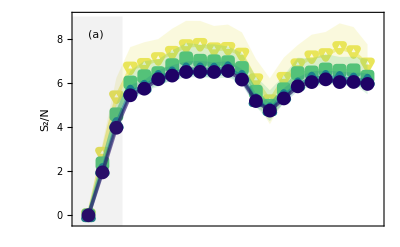
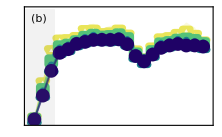
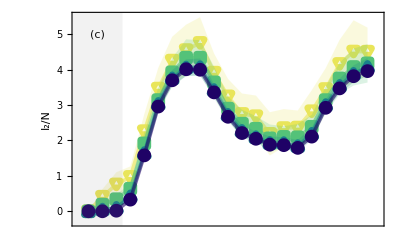
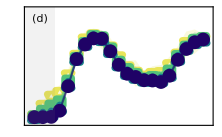
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- |  |  |  Amplitude noise Δ_ξ=ξδ    Phase noise Δ_Φ=δ

```mathematica
Fig6LowFreqErrorPlot[data1_,data2_,data3_,dataNoErrors_,letterTitle_,entropicMeasure_]:=Module[
{tFlag={}, meanFlag={},stddevFlag={},
upperFlag={},lowerFlag={},shadeFlag={}},

(* Extract components. *)
tFlag={data1[[All,1]],data2[[All,1]],data3[[All,1]]};
meanFlag={data1[[All,2]],data2[[All,2]],data3[[All,2]]};
stddevFlag={data1[[All,3]],data2[[All,3]],data3[[All,3]]};

(* Create upper and lower bounds for the shaded regions. *)
upperFlag=meanFlag+stddevFlag;
lowerFlag=meanFlag-stddevFlag;

(* Create polygons for the shaded area. *)
shadeFlag={Polygon[Join[Transpose[{tFlag[[1]],upperFlag[[1]]}],Reverse[Transpose[{tFlag[[1]],lowerFlag[[1]]}]]]],
Polygon[Join[Transpose[{tFlag[[2]],upperFlag[[2]]}],Reverse[Transpose[{tFlag[[2]],lowerFlag[[2]]}]]]],
Polygon[Join[Transpose[{tFlag[[3]],upperFlag[[3]]}],Reverse[Transpose[{tFlag[[3]],lowerFlag[[3]]}]]]]};

(* Plot everything. *)
Show[ListLinePlot[Transpose[{tFlag[[1]],meanFlag[[1]]}],
PlotRange->{{-0.15,4.15},
{-0.3,If[entropicMeasure==1,9.0,
If[entropicMeasure==2,5.5]]}},
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->Fig6PlotStyles[[1]],
FrameLabel->{None,
If[entropicMeasure==1&&ToString[letterTitle]=="a",Style["S_2/N",Black,FontSize->18],
If[entropicMeasure==2&&ToString[letterTitle]=="c",Style["I_2/N",Black,FontSize->18],
None]]},
FrameTicks->{{If[entropicMeasure==1,
If[ToString[letterTitle]=="a",{0,2,4,6,8},None],
If[entropicMeasure==2,
If[ToString[letterTitle]=="c",{0,1,2,3,4,5},None]]],None},
{None,None}}, 
FrameStyle->Directive[Black,Thickness[0.005]],
FrameTicksStyle->Directive[Black,FontSize->16],
GridLines->None], 
ListPlot[Transpose[{tFlag[[1]],meanFlag[[1]]}],PlotMarkers->Fig6PlotMarkers[[1]]],
Graphics[{ContinuousColors[0.8,0][0.],Opacity[0.2],shadeFlag[[1]]}],
(***********)
ListLinePlot[Transpose[{tFlag[[2]],meanFlag[[2]]}],
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->Fig6PlotStyles[[2]],
GridLines->None],
ListPlot[Transpose[{tFlag[[2]],meanFlag[[2]]}],PlotMarkers->Fig6PlotMarkers[[2]]],
Graphics[{ContinuousColors[0.8,0][0.8/3],Opacity[0.2],shadeFlag[[2]]}],
(***********)
ListLinePlot[Transpose[{tFlag[[3]],meanFlag[[3]]}],
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->Fig6PlotStyles[[3]],
GridLines->None],
ListPlot[Transpose[{tFlag[[3]],meanFlag[[3]]}],PlotMarkers->Fig6PlotMarkers[[3]]],
Graphics[{ContinuousColors[0.8,0][2*0.8/3],Opacity[0.2],shadeFlag[[3]]}],
(***********)
(* We also plot the points without errors. *) 
ListLinePlot[Transpose[{dataNoErrors[[All,1]],Flatten[dataNoErrors[[All,2]]]}],
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->{Thickness[0.0065],ContinuousColors[0.8,0][0.8],Opacity[0.6]},
GridLines->None],
ListPlot[Transpose[{dataNoErrors[[All,1]],Flatten[dataNoErrors[[All,2]]]}],
PlotMarkers->Fig6PlotMarkers[[4]]],
(***********)
Graphics[{Black,FontSize->14,
If[ToString[letterTitle]=="a",
Style[Text["("<>ToString[letterTitle]<>")",
If[entropicMeasure==1,{0.1,8.2},
If[entropicMeasure==2,{0.13,5.0}]]],Bold],
If[ToString[letterTitle]=="b",
Style[Text["("<>ToString[letterTitle]<>")",
If[entropicMeasure==1,{0.1,8.2},
If[entropicMeasure==2,{0.13,5.0}]]],Bold],
If[ToString[letterTitle]=="c",
Style[Text["("<>ToString[letterTitle]<>")",
If[entropicMeasure==1,{0.1,8.2},
If[entropicMeasure==2,{0.13,5.0}]]],Bold],
If[ToString[letterTitle]=="d",
Style[Text["("<>ToString[letterTitle]<>")",
If[entropicMeasure==1,{0.1,8.2},
If[entropicMeasure==2,{0.13,5.0}]]],Bold]]]]],
Gray,Opacity[0.1], (* ! *)
Rectangle[{-1,-1},{τ[25,5,1,2],9}]}],
(***********)
Epilog->{If[entropicMeasure==1&&ToString[letterTitle]=="a",
Inset[IntensityErrorGraph,
Scaled[{0.85,0.3}],Center,
(* scale relative to main plot size *)
Scaled[{0.4,0.4}]],
If[entropicMeasure==1&&ToString[letterTitle]=="b",
Inset[AngleErrorGraph,
Scaled[{0.85,0.3}],Center,
Scaled[{0.35,0.35}]]]]},
(* For the manuscript: *)
If[ToString[letterTitle]=="a",
ImageSize->{Automatic,141.5},
If[ToString[letterTitle]=="b",
ImageSize->{222,Automatic},
If[ToString[letterTitle]=="c",
ImageSize->{Automatic,139},
If[ToString[letterTitle]=="d",
ImageSize->{222,Automatic}]]]]]]

(*******************************)

Clear[a,b,c,d];
Fig6a=Fig6LowFreqErrorPlot[Renyi2SimulatorLowFreqErrorIntensityData[[3]][[1]],
Renyi2SimulatorLowFreqErrorIntensityData[[2]][[1]],
Renyi2SimulatorLowFreqErrorIntensityData[[1]][[1]],
Renyi2SimulatorIdealData[[1]],a,1];
Fig6b=Fig6LowFreqErrorPlot[Renyi2SimulatorLowFreqErrorAngleData[[3]][[1]],
Renyi2SimulatorLowFreqErrorAngleData[[2]][[1]],
Renyi2SimulatorLowFreqErrorAngleData[[1]][[1]],
Renyi2SimulatorIdealData[[1]],b,1];
Fig6c=Fig6LowFreqErrorPlot[Renyi2SimulatorLowFreqErrorIntensityData[[3]][[2]],
Renyi2SimulatorLowFreqErrorIntensityData[[2]][[2]],
Renyi2SimulatorLowFreqErrorIntensityData[[1]][[2]],
Renyi2SimulatorIdealData[[2]],c,2];
Fig6d=Fig6LowFreqErrorPlot[Renyi2SimulatorLowFreqErrorAngleData[[3]][[2]],
Renyi2SimulatorLowFreqErrorAngleData[[2]][[2]],
Renyi2SimulatorLowFreqErrorAngleData[[1]][[2]],
Renyi2SimulatorIdealData[[2]],d,2];

GridFig6LowFreqError=Labeled[Legended[Grid[{{
Grid[{{Fig6a,Fig6b,,,}},
Alignment->{{Top,Bottom},{Top,Bottom}},
Spacings->0.4]},
{Grid[{{Fig6c,Fig6d,,,}},
Alignment->{{Top,Bottom},{Top,Bottom}},
Spacings->0.4]}},
Alignment->{{Top,Bottom},{Top,Bottom}},
Spacings->{0,0.1}],
Placed[Rotate[Style[Text["Low frequency"],18,Black],-Pi/2],{1,0.5}]],
Row[{Style[Text[" Amplitude noise Δ_ξ=ξδ    "],18,Black],
Spacer[40],
Style[Text["Phase noise Δ_Φ=δ    "],18,Black]}], 
{{Top,Center}}]
```

#### High frequency error

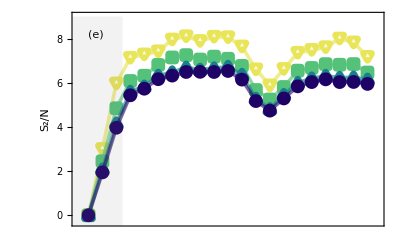
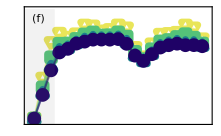
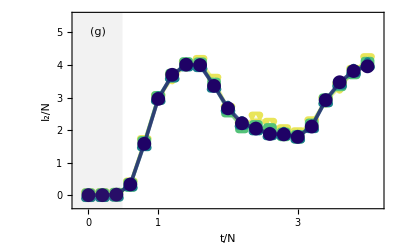
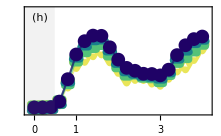
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- |  |  |

```mathematica
Fig6HighFreqErrorPlot[data1_,data2_,data3_,dataNoErrors_,letterTitle_,entropicMeasure_]:=Module[
{tFlag={}, meanFlag={},stddevFlag={},
upperFlag={},lowerFlag={},shadeFlag={}},

(* Extract components. *)
tFlag={data1[[All,1]],data2[[All,1]],data3[[All,1]]};
meanFlag={data1[[All,2]],data2[[All,2]],data3[[All,2]]};
stddevFlag={data1[[All,3]],data2[[All,3]],data3[[All,3]]};

(* Create upper and lower bounds for the shaded regions. *)
upperFlag=meanFlag+stddevFlag;
lowerFlag=meanFlag-stddevFlag;

(* Create polygons for the shaded area. *)
shadeFlag={Polygon[Join[Transpose[{tFlag[[1]],upperFlag[[1]]}],Reverse[Transpose[{tFlag[[1]],lowerFlag[[1]]}]]]],
Polygon[Join[Transpose[{tFlag[[2]],upperFlag[[2]]}],Reverse[Transpose[{tFlag[[2]],lowerFlag[[2]]}]]]],
Polygon[Join[Transpose[{tFlag[[3]],upperFlag[[3]]}],Reverse[Transpose[{tFlag[[3]],lowerFlag[[3]]}]]]]};

(* Plot everything. *)
Show[ListLinePlot[Transpose[{tFlag[[1]],meanFlag[[1]]}],
PlotRange->{{-0.15,4.15},
{-0.3,If[entropicMeasure==1,9.0,
If[entropicMeasure==2,5.5]]}},
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->Fig6PlotStyles[[1]],
FrameLabel->{If[ToString[letterTitle]=="e"||ToString[letterTitle]=="f",None,
If[ToString[letterTitle]=="g"||ToString[letterTitle]=="h",Style["t/N",Black,FontSize->18]]],
If[entropicMeasure==1&&ToString[letterTitle]=="e",Style["S_2/N",Black,FontSize->18],
If[entropicMeasure==2&&ToString[letterTitle]=="g",Style["I_2/N",Black,FontSize->18],
None]]},
FrameTicks->{{If[entropicMeasure==1,
If[ToString[letterTitle]=="e",{0,2,4,6,8},None],
If[entropicMeasure==2,
If[ToString[letterTitle]=="g",{0,1,2,3,4,5},None]]],None},
{If[ToString[letterTitle]=="e"||ToString[letterTitle]=="f",None,
If[ToString[letterTitle]=="g"||ToString[letterTitle]=="h",{0,{τ[25,5,1,2],"τ/N"},1,2,3,4}]],None}},
FrameStyle->Directive[Black,Thickness[0.005]],
FrameTicksStyle->Directive[Black,FontSize->16],
GridLines->None],
ListPlot[Transpose[{tFlag[[1]],meanFlag[[1]]}],PlotMarkers->Fig6PlotMarkers[[1]]],
Graphics[{ContinuousColors[0.8,0][0.],Opacity[0.2],shadeFlag[[1]]}],
(***********)
ListLinePlot[Transpose[{tFlag[[2]],meanFlag[[2]]}],
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->Fig6PlotStyles[[2]],
GridLines->None],
ListPlot[Transpose[{tFlag[[2]],meanFlag[[2]]}],PlotMarkers->Fig6PlotMarkers[[2]]],
Graphics[{ContinuousColors[0.8,0][0.8/3],Opacity[0.2],shadeFlag[[2]]}],
(***********)
ListLinePlot[Transpose[{tFlag[[3]],meanFlag[[3]]}],
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->Fig6PlotStyles[[3]],
GridLines->None],
ListPlot[Transpose[{tFlag[[3]],meanFlag[[3]]}],PlotMarkers->Fig6PlotMarkers[[3]]],
Graphics[{ContinuousColors[0.8,0][2*0.8/3],Opacity[0.2],shadeFlag[[3]]}],
(***********)
(* We also plot the points without errors. *) 
ListLinePlot[Transpose[{dataNoErrors[[All,1]],Flatten[dataNoErrors[[All,2]]]}],
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->{Thickness[0.0065],ContinuousColors[0.8,0][0.8],Opacity[0.6]},
GridLines->None],
ListPlot[Transpose[{dataNoErrors[[All,1]],Flatten[dataNoErrors[[All,2]]]}],
PlotMarkers->Fig6PlotMarkers[[4]]],
(***********)
Graphics[{Black,FontSize->14,
If[ToString[letterTitle]=="e",
Style[Text["("<>ToString[letterTitle]<>")",
If[entropicMeasure==1,{0.1,8.2},
If[entropicMeasure==2,{0.13,5.0}]]],Bold],
If[ToString[letterTitle]=="f",
Style[Text["("<>ToString[letterTitle]<>")",
If[entropicMeasure==1,{0.1,8.2},
If[entropicMeasure==2,{0.13,5.0}]]],Bold],
If[ToString[letterTitle]=="g",
Style[Text["("<>ToString[letterTitle]<>")",
If[entropicMeasure==1,{0.1,8.2},
If[entropicMeasure==2,{0.13,5.0}]]],Bold],
If[ToString[letterTitle]=="h",
Style[Text["("<>ToString[letterTitle]<>")",
If[entropicMeasure==1,{0.1,8.2},
If[entropicMeasure==2,{0.13,5.0}]]],Bold]]]]],
Gray,Opacity[0.1], (* ! *)
Rectangle[{-1,-1},{τ[25,5,1,2],9}]}],
(***********)
(* For the manuscript: *)
If[ToString[letterTitle]=="e",
ImageSize->{Automatic,141.5},
If[ToString[letterTitle]=="f",
ImageSize->{221.5,Automatic},
If[ToString[letterTitle]=="g",
ImageSize->{Automatic,184},
If[ToString[letterTitle]=="h",
ImageSize->{221.5,Automatic}]]]]]]

(*******************************)

Clear[e,f,g,h];
Fig6e=Fig6HighFreqErrorPlot[Renyi2SimulatorHighFreqErrorIntensityData[[3]][[1]],
Renyi2SimulatorHighFreqErrorIntensityData[[2]][[1]],
Renyi2SimulatorHighFreqErrorIntensityData[[1]][[1]],
Renyi2SimulatorIdealData[[1]],e,1];
Fig6f=Fig6HighFreqErrorPlot[Renyi2SimulatorHighFreqErrorAngleData[[3]][[1]],
Renyi2SimulatorHighFreqErrorAngleData[[2]][[1]],
Renyi2SimulatorHighFreqErrorAngleData[[1]][[1]],
Renyi2SimulatorIdealData[[1]],f,1];
Fig6g=Fig6HighFreqErrorPlot[Renyi2SimulatorHighFreqErrorIntensityData[[3]][[2]],
Renyi2SimulatorHighFreqErrorIntensityData[[2]][[2]],
Renyi2SimulatorHighFreqErrorIntensityData[[1]][[2]],
Renyi2SimulatorIdealData[[2]],g,2];
Fig6h=Fig6HighFreqErrorPlot[Renyi2SimulatorHighFreqErrorAngleData[[3]][[2]],
Renyi2SimulatorHighFreqErrorAngleData[[2]][[2]],
Renyi2SimulatorHighFreqErrorAngleData[[1]][[2]],
Renyi2SimulatorIdealData[[2]],h,2];

GridFig6HighFreqError=Legended[Grid[{{
Grid[{{Fig6e,Fig6f,,,}},
Alignment->{{Top,Bottom},{Top,Bottom}},
Spacings->0.4,
Alignment->{{Top,Bottom},{Top,Bottom}}]},
{Grid[{{Fig6g,Fig6h,,,}},
Alignment->{{Top,Bottom},{Top,Bottom}},
Spacings->0.4,
Alignment->{{Top,Bottom},{Top,Bottom}}]}},
Alignment->{{Top,Bottom},{Top,Bottom}},
Spacings->{0,0.1}],
Placed[Rotate[Style[Text["High frequency"],Bold,18,Black],-Pi/2],{1,0.6}]]
```

### Final figure

```mathematica
(* Combine the latter plots with a bar legend. *)
LegendBarFig6=Rasterize[BarLegend[{ContinuousColors[0.01,0.8],{0.01,0.8}},
LabelStyle->{Black,FontSize->14},
LegendMarkerSize->200,
Ticks->{{0.01,"0.0"},{0.8/3,"0.1"},{2*0.8/3,"0.2"},{0.8,"0.3"}},
LegendLabel->Style[Text["δ"],FontSize->18,Black]],
ImageResolution->300,ImageSize->60] ;

Fig6=Rasterize[Legended[Grid[{{GridFig6LowFreqError,,,,,,,,,,,,,,,,},
{GridFig6HighFreqError}},
Alignment->{{Center},{Center}},
Spacings->{0,0.3}],
Placed[LegendBarFig6,{1.,0.55}]],
ImageResolution->300]
```

-Graphics-

```mathematica
(* To export the pdf. *)
(* Export[FileNameJoin[{"NoiseStatePreparation.pdf"}],Fig6,ImageResolution->Automatic,"AllowRasterization"->True] *)
```

NoiseStatePreparation.pdf

Fig. 7

### Importing and generating data

```mathematica
(* Set directory to the notebook directory. *)
SetDirectory[NotebookDirectory[]];

(* Data generated by means of the repository https://github.com/alexn2002/LoGIC
This repository takes covariance matrices as input and evolves them under an interferometer layer. Such a layer is decomposed with Clements (square) and Reck (triangular) decompositions and symmetric loss is applied after every beam splitter by means of beam splitters of transmissivity T, coupling the input state with the vacuum. *)

(* In what follows we considered T to be 0.98. Please check that the downloaded files from our repository are contained in the same directory in which this notebook is. *)
LossyCovMatClementsT098=Import["Clements098.wl","WL"];
LossyCovMatReckT098=Import["Reck098.wl","WL"];
```

```mathematica
(* Ideal case used for comparison was already computed for Fig.6.
Uncomment what follows if you are only interested in Fig.7. *)

(* Renyi2SimulatorIdealData={Renyi2EntanglementEntropySimulator[100,5,25,5,2,1,2.0],Renyi2MutualInformationSimulator[100,5,25,5,5,2,1,2.0]}; *)
```

### Generating entropic measures with loss

```mathematica
EntropicMeasuresWithLoss[time_,timePoints_,ModeNumber_,MSize_,Distance_,data_]:=Module[
{tInt=0.,Renyi2LossTablePlot={},MILossTablePlot={},
Renyi2LossTablePlotEnd={},MILossTablePlotEnd={}},

Clear[k];
For[k=1,k<=timePoints+1,k++,
AppendTo[Renyi2LossTablePlot,{tInt/ModeNumber,100*Renyi2EntanglementEntropyGaussian[data[[k]],MSize]/ModeNumber}];
AppendTo[MILossTablePlot,{tInt/ModeNumber,100*Renyi2MutualInformationGaussian[data[[k]],MSize,Distance]/ModeNumber}];
AppendTo[Renyi2LossTablePlotEnd,{tInt/ModeNumber,100*Renyi2EntanglementEntropyGaussianFromEnd[data[[k]],MSize]/ModeNumber}];
AppendTo[MILossTablePlotEnd,{tInt/ModeNumber,100*Renyi2MutualInformationGaussianFromEnd[data[[k]],MSize,Distance]/ModeNumber}];
tInt+=time/timePoints];

{Chop[Renyi2LossTablePlot],Chop[MILossTablePlot],Chop[Renyi2LossTablePlotEnd],Chop[MILossTablePlotEnd]}]

EntropicMeasuresClementsT098Data=EntropicMeasuresWithLoss[100,20,25,5,5,LossyCovMatClementsT098];
EntropicMeasuresReckT098Data=EntropicMeasuresWithLoss[100,20,25,5,5,LossyCovMatReckT098];
```

### Individual plots

#### Inset and legend

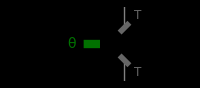

```mathematica
BSGraph=Graphics[{{Thick,GrayLevel[0.5],
(*Outputs after loss BS*)
Line[{{6,1},{6,3}}],
Line[{{6,-1},{6,-3}}]},
{Thick,Black,
(*Input beams*)
Line[{{1,1},{3,1}}],Line[{{1,-1},{3,-1}}],
(*Connections into central BS*)
Line[{{3,1},{4,0}}],Line[{{3,-1},{4,0}}],
(*Outputs from central BS*)
Line[{{5,1},{4,0}}],Line[{{5,-1},{4,0}}],
(*Outputs after loss BS*)
Line[{{5,1},{7.5,1}}],Line[{{5,-1},{7.5,-1}}],
(*Central beam splitter plate*)
{AbsoluteThickness[6],RGBColor[1/255,113/255,0],Line[{{3.5,0},{4.5,0}}]},
(*Loss BS plates on each output*)
{AbsoluteThickness[4],GrayLevel[0.4],Line[{{6.3,1.3},{5.7,0.7}}]},
{AbsoluteThickness[4],GrayLevel[0.4],Line[{{5.7,-0.7},{6.3,-1.3}}]},
Text[Style["θ",RGBColor[1/255,113/255,0],14],{2.75,0.}],
Text[Style["T",GrayLevel[0.4],12],{6.8,1.75}],
Text[Style["T",GrayLevel[0.4],12],{6.8,-1.75}]}},
PlotRange->{{-0.5,9.5},{-2.2,2.2}},
AspectRatio->Automatic,
ImageSize->200,
Background->Transparent]
```

```mathematica
downTriangleDec=Graphics[{ContinuousColors[0.8,0][0.],Polygon[{{0,1},{1,1},{0.5,0}}]},ImageSize->12,PlotRange->{{0,1},{0,1}},BaselinePosition->Scaled[.15]];
SquareDec=Graphics[{ContinuousColors[0.8,0][0.8/3],Rectangle[]},ImageSize->12,BaselinePosition->Scaled[.15]];
upTriangleDec=Graphics[{ContinuousColors[0.8,0][2*0.8/3],Polygon[{{0.5,1},{0,0},{1,0}}]},ImageSize->12,PlotRange->{{0,1},{0,1}},BaselinePosition->Scaled[.05]];
IdealCase=Graphics[{ContinuousColors[0.8,0][0.8],Disk[{0,0},1]},ImageSize->12,PlotRange->Automatic,BaselinePosition->Scaled[.2]];
```

#### Entropic measures with loss

```mathematica
Fig7Plot[data_,dataClements_,dataNoErrors_,letterTitle_,entropicMeasure_]:=Module[
{tFlag={},S2Flag={},MI2Flag={},
S2EndFlag={},MI2EndFlag={},
S2ClementsFlag={},MI2ClementsFlag={},
tFlagNoLoss={},S2FlagNoLoss={},MI2FlagNoLoss={}},

(* Extract components *)
tFlag={data[[1]][[All,1]]};
S2Flag={data[[1]][[All,2]]};
MI2Flag={data[[2]][[All,2]]};
S2EndFlag={data[[3]][[All,2]]};
MI2EndFlag={data[[4]][[All,2]]};

S2ClementsFlag={dataClements[[1]][[All,2]]};
MI2ClementsFlag={dataClements[[2]][[All,2]]};

tFlagNoLoss=dataNoErrors[[1]][[All,1]];
S2FlagNoLoss=dataNoErrors[[1]][[All,2]];
MI2FlagNoLoss=dataNoErrors[[2]][[All,2]];

(* Plot mean line and shaded area *)
(* Plot Reck first modes. *) 
Show[ListLinePlot[Transpose[{tFlag[[1]],
If[entropicMeasure==1,
S2EndFlag[[1]],
MI2EndFlag[[1]]]}],
PlotRange->{{-0.15,4.15},
{-0.3,If[entropicMeasure==1,7.5,
If[entropicMeasure==2,4.5]]}},
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->{Thickness[0.0065],ContinuousColors[0.8,0][0.],Opacity[0.6]},
FrameLabel->{If[ToString[letterTitle]=="a",None,
If[ToString[letterTitle]=="b",Style["t/N",Black,FontSize->15]]],
If[entropicMeasure==1&&ToString[letterTitle]=="a",Style["S_2/N",Black,FontSize->15],
If[entropicMeasure==2&&ToString[letterTitle]=="b",Style["I_2/N",Black,FontSize->15]]]},
FrameTicks->{{If[entropicMeasure==1,
If[ToString[letterTitle]=="a",{0,2,4,6,8},None],
If[entropicMeasure==2,
If[ToString[letterTitle]=="b",{0,1,2,3,4,5},None]]],None},
{If[ToString[letterTitle]=="a",None,
If[ToString[letterTitle]=="b",{0,{τ[25,5,1,2],"τ/N"},1,2,3,4}]],None}},
FrameStyle->Directive[Black,Thickness[0.005]],
FrameTicksStyle->Directive[Black,FontSize->14],
GridLines->None],
ListPlot[Transpose[{tFlag[[1]],
If[entropicMeasure==1,S2EndFlag[[1]],MI2EndFlag[[1]]]}],
PlotMarkers->Fig7PlotMarkers[[1]]],
(***********)
(* Plot Clements first modes. *) 
ListLinePlot[Transpose[{tFlag[[1]],
If[entropicMeasure==1,
S2ClementsFlag[[1]],
MI2ClementsFlag[[1]]]}],
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->{Thickness[0.0065],ContinuousColors[0.8,0][0.8/3],Opacity[0.6]}],
ListPlot[Transpose[{tFlag[[1]],
If[entropicMeasure==1,S2ClementsFlag[[1]],MI2ClementsFlag[[1]]]}],
PlotMarkers->Fig7PlotMarkers[[2]]],
(***********)
(* Plot Reck last modes. *) 
ListLinePlot[Transpose[{tFlag[[1]],
If[entropicMeasure==1,
S2Flag[[1]],
MI2Flag[[1]]]}],
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->{Thickness[0.0065],ContinuousColors[0.8,0][2*0.8/3],Opacity[0.6]}],
ListPlot[Transpose[{tFlag[[1]],
If[entropicMeasure==1,S2Flag[[1]],MI2Flag[[1]]]}],
PlotMarkers->Fig7PlotMarkers[[3]]],
(***********)
(* We also plot the points without errors. *) 
ListLinePlot[Transpose[{tFlagNoLoss,If[entropicMeasure==1,
S2FlagNoLoss,
MI2FlagNoLoss]}],
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->{Thickness[0.0065],ContinuousColors[0.8,0][0.8],Opacity[0.6]},
GridLines->None],
ListPlot[Transpose[{tFlagNoLoss,If[entropicMeasure==1,S2FlagNoLoss,MI2FlagNoLoss]}],
PlotMarkers->Fig7PlotMarkers[[4]]],
(***********)
Graphics[{Black,FontSize->15,
Style[Text["("<>ToString[letterTitle]<>")",
If[entropicMeasure==1,{0.1,6.8},
If[entropicMeasure==2,{0.13,4.0}]]],Bold],
Gray,Opacity[0.1], (* ! *)
Rectangle[{-1,-1},{τ[25,5,1,2],7.5}]}],
(***********)
Epilog->{If[entropicMeasure==1,
Inset[BSGraph,
(* position of the beam splitter. *)
Scaled[{0.8,0.25}],Center,
(* scale relative to main plot size. *)
Scaled[{0.5,0.5}]]]},
(* For the manuscript: *)
ImageSize->{Automatic,If[ToString[letterTitle]=="a",179.6,220]}]]
```

### Final figure

```mathematica
Fig7a=Fig7Plot[EntropicMeasuresReckT098Data,
EntropicMeasuresClementsT098Data,
Renyi2SimulatorIdealData,a,1];

Fig7b=Fig7Plot[EntropicMeasuresReckT098Data,
EntropicMeasuresClementsT098Data,
Renyi2SimulatorIdealData,b,2];

Fig7=Rasterize[Legended[Grid[{{
Grid[{{Fig7a,,,,,,,,}}]},
{Grid[{{Fig7b,,,,,,,,}}]}},
Alignment->{{Top,Bottom},{Top,Bottom}}],
Placed[Column[{Row[{IdealCase,Style[Text[" Ideal"],16]}],
"     ",
Row[{upTriangleDec,Style[Text[" R"],16]}],
"     ",
Row[{SquareDec,Style[Text[" C"],16]}],
"     ",
Row[{downTriangleDec,Style[Text[" R"],16]}]}],
{0.97,0.58}]],ImageResolution->300]
```

-Graphics-

```mathematica
(* To export the pdf. *)
(* Export[FileNameJoin[{"Loss.pdf"}],Fig7,ImageResolution->Automatic,"AllowRasterization"->True] *)
```

Loss.pdf

Fig. 10

### OBC relativistic theory and its dispersion relation

```mathematica
RelativisticHamiltonianMatrixOBC[n_,m_,ϵ_]:=Module[
{Hϕ,ν,μ,eps=N[ϵ]},
ν=-1/eps;
μ=eps*(m^2)-2*ν;

(* Let us define a tridiagonal matrix. *)
Hϕ=DiagonalMatrix[ArrayFlatten[{μ+ν,ConstantArray[μ,n-2],μ+ν},1]]
+DiagonalMatrix[ConstantArray[ν,n-1],1]
+DiagonalMatrix[ConstantArray[ν,n-1],-1];

Simplify[Hϕ]]

(* First appearance of correlations. Divided by n already! *)
τOBC[n_,M_,m_,ϵ_]:=(M*ϵ)/(2*n*vmaxOBC[M,m,ϵ]);
```

```mathematica
(* Maximum quasi-particle velocity. Not needed in the following. *)
vmaxOBC[n_,m_,ϵ_]:=Module[{ωFlag,vList={},vMaxFlag},
ωFlag[i_]:=N[Sqrt[m^2+(4/ϵ^2)*Sin[π*(i-1)/(2*n)]^2]];
vList=Table[Sin[π*(k-1)/n]/(ϵ*ωFlag[k]),{k,1,n}]; (* sligthly different from PBC. *)
vMaxFlag=Max[vList];
vMaxFlag];
```

### Covariance matrix

```mathematica
(* The following function generates the time evolution of the covariance matrix by means of the OTA for the OBC relativistic theory. *)
TimeEvolutionCovarianceMatrixOBC[t_,Δt_,n_,m_,ϵ_]:= Module[
{Hϕ,Hπ,EigenValHϕ, EigenVecHϕ,
GammaNEigenVal,GammaN,
NewEigenVec= {},
TallyFlag, PositionFlag,
OrthogonalZ,BlockTN,
BN, AN,SSD,
InvBN,InvAN,InvSSD,
SymplecticEigenVal,DN,WilliamsonD,
PSTimeEvo,
SSDProduct,
TimeEvolutionCovMat,
CovMatTable,i},

(* Hamiltonian matrix. *)
 Hϕ = RelativisticHamiltonianMatrixOBC[n,m,ϵ];
 
Hπ = IdentityMatrix[n]/ϵ;

(* Eigenvectors and eigenvalues of Hϕ. *)
{EigenValHϕ, EigenVecHϕ} = Re[Eigensystem[Hϕ]];

(* Diagonal matrix ΓN. *)
GammaNEigenVal=Sqrt[ϵ*EigenValHϕ];
GammaN=DiagonalMatrix[GammaNEigenVal];

(* Symplectic eigenvalues and the corresponding diagonal matrix. *)
SymplecticEigenVal=EigenValHϕ/GammaNEigenVal;
DN=DiagonalMatrix[SymplecticEigenVal];
WilliamsonD=ArrayFlatten[{{DN,0},{0,DN}}] ;

(* Orthogonal set of eigenvectors (in a given subspace with degenerate eigenvalues). *)
TallyFlag = Tally[EigenValHϕ,Abs[#1-#2]<10^(-10)&];
For[i=1, i<=Length[TallyFlag], i++,
PositionFlag=Flatten[Position[EigenValHϕ,_?(Abs[#-TallyFlag[[i]][[1]]]<10^(-10)&)]];
If[TallyFlag[[i]][[2]]==1,
AppendTo[NewEigenVec, EigenVecHϕ[[PositionFlag[[1]]]]],
OrthogonalZ = Orthogonalize[{EigenVecHϕ[[PositionFlag[[1]]]], EigenVecHϕ[[PositionFlag[[2]]]]}, Dot];
AppendTo[NewEigenVec,OrthogonalZ[[1]]];
AppendTo[NewEigenVec, OrthogonalZ[[2]]]]];

(* T given by the polar decomposition. *)
BlockTN = Normalize/@NewEigenVec;

(* Normalize the orthogonal eigenvectors to define BN. *)
BN = Sqrt[GammaNEigenVal]*BlockTN;

(* Define A and SSD matrices. *)
AN = -Inverse[GammaN].BN;
SSD = ArrayFlatten[{{BN,0},{0,-AN}}] ;

(* Invert matrices. *)
InvBN=Transpose[BN].Inverse[GammaN];
InvAN=Transpose[AN].GammaN;
InvSSD=ArrayFlatten[{{InvBN,0},{0,-InvAN}}] ;

(* SSD product appearing in the middle of the time-evolved covariance matrix. *)
SSDProduct=ArrayFlatten[{{GammaN,0},{0,Inverse[GammaN]}}];

(* PS in the middle of the decomposition. *)
PSTimeEvo[tFlag_]:=MatrixExp[tFlag*SymplecticForm[n].WilliamsonD];

(* Time-evolved covariance matrix for vacuum input. *)
TimeEvolutionCovMat[tFlag_]:=Chop[0.5*InvSSD.PSTimeEvo[tFlag].SSDProduct.Transpose[InvSSD.PSTimeEvo[tFlag]]];

CovMatTable=Table[TimeEvolutionCovMat[tInt],{tInt,0,t,Δt}]]
```

### Entropic measures

#### Photonic simulation

```mathematica
(* The same entropic measures for the photonic simulation with fractional Laplacian theory input parameters. *)
Renyi2EntanglementEntropySimulatorOBC[t_,Δt_,n_,M_,m_,ϵ_]:=Module[{data=TimeEvolutionCovarianceMatrixOBC[t,Δt,n,m,ϵ]},
Table[{Δt*(tInt-1)/n,100*Renyi2EntanglementEntropyGaussian[data[[tInt]],M]/n},{tInt,1,Length[data]}]];

Renyi2MutualInformationSimulatorOBC[t_,Δt_,n_,M_,d_,m_,ϵ_]:=Module[{data=TimeEvolutionCovarianceMatrixOBC[t,Δt,n,m,ϵ]},
Table[{Δt*(tInt-1)/n,100*Renyi2MutualInformationGaussian[data[[tInt]],M,d]/n},{tInt,1,Length[data]}]];
```

#### QFT prediction

```mathematica
(* Rényi-2 entanglement entropy of the relativistic theory following the quasi-particle picture. *)
(* The main difference with the PBC is that now the translational symmetry is broken. *)
Renyi2EntanglementEntropyQFTwOBC[t_,n_,M_,m_,ϵ_]:=Module[
{DispertionRelationOBC, GroupVelocityOBC,NumberQPwOBC,GGEDensityEntropyOBC,
Part1OBC,Part2OBC,Part3OBC,DomainOBC,
ToBeSummedEEwOBC,
FinalEEwOBC},

(* Building block functions. *)
DispertionRelationOBC[k_]:=Sqrt[m^2+4*(Sin[π*k/(2*n)]/ϵ)^2];
GroupVelocityOBC[k_]:=Abs[Sin[π*k/n]/(ϵ*DispertionRelationOBC[k])];
NumberQPwOBC[k_]:=Simplify[(1/(ϵ*DispertionRelationOBC[k])+ (ϵ*DispertionRelationOBC[k])-2)/4];
(* If the number of quasiparticles is zero for some mode, the entanglement is also zero. *)
GGEDensityEntropyOBC[k_]:=If[NumberQPwOBC[k]!=0,Simplify[Log[-NumberQPwOBC[k]^2+(1+NumberQPwOBC[k])^2]],0];

(* Function to be summed. *)
DomainOBC[k_]:=FractionalPart[GroupVelocityOBC[k]*t/(n*ϵ)]; (* slightly different. *)
Part1OBC[k_]:=GGEDensityEntropyOBC[k]*DomainOBC[k];
Part2OBC[k_]:=(M/n)*GGEDensityEntropyOBC[k];
Part3OBC[k_]:=GGEDensityEntropyOBC[k]*(1-DomainOBC[k]);

ToBeSummedEEwOBC[k_]:=Piecewise[{{Part1OBC[k],DomainOBC[k]<M/n},
{Part2OBC[k],M/n<=DomainOBC[k]<1-M/n},
{Part3OBC[k],DomainOBC[k]>=1-M/n}}]; 

FinalEEwOBC=Simplify[Sum[ToBeSummedEEwOBC[k],{k,0,n-1}]]];
```

```mathematica
(* The same for the Rényi-2 mutual information. *)
(* In the OBC case, one also needs the number of modes d1 separating the first region from the wall. *)
Renyi2MutualInformationQFTwOBC[t_,n_,M_,d_,d1_,m_,ϵ_]:=Module[
{d2,
DispertionRelationOBC, 
GroupVelocityOBC,
NumberQP,GGEDensityEntropy,
Part1,PartA,PartB,PartC,
PartA2,PartB2,PartC2,
DomainV,DomainDA,DomainDB,DomainDC,
ToBeSummedMI,
FinalMI},

(* Building block functions. *)
d2=n-2*M-d-d1;

DispertionRelationOBC[k_]:=Sqrt[m^2+4*(Sin[π*k/(2*n)]/ϵ)^2];
GroupVelocityOBC[k_]:=Abs[Sin[π*k/n]]/(ϵ*DispertionRelationOBC[k]);
NumberQP[k_]:=Simplify[(1/(ϵ*DispertionRelationOBC[k])+ (ϵ*DispertionRelationOBC[k])-2)/4];
GGEDensityEntropy[k_]:=If[NumberQP[k]!=0,Simplify[Log[-NumberQP[k]^2+(1+NumberQP[k])^2]],0];

(* Functions to be summed. *)
(* We want vt=2L to be the condition to reach the initial condition. *)
DomainV[k_]:=FractionalPart[GroupVelocityOBC[k]*t/(n*ϵ)];  
(* DomainV[k_]:=FractionalPart[GroupVelocityOBC[k]*t/(n*ϵ)]; *)

DomainDA[distance_]:=distance/(2*n);
DomainDB[distance_]:=(distance+2*M)/(2*n);
DomainDC[distance_]:=(distance+M)/(2*n);

Part1[k_]:=DomainV[k]*GGEDensityEntropy[k];

PartA2[k_,distance_]:=DomainDA[distance]*GGEDensityEntropy[k];
PartA[k_,distance_]:=Piecewise[{{Part1[k],DomainV[k]>DomainDA[distance]},
{PartA2[k,distance],DomainV[k]<=DomainDA[distance]}}];

PartB2[k_,distance_]:=DomainDB[distance]*GGEDensityEntropy[k];
PartB[k_,distance_]:=Piecewise[{{Part1[k],DomainV[k]>DomainDB[distance]},
{PartB2[k,distance],DomainV[k]<=DomainDB[distance]}}];

PartC2[k_,distance_]:=DomainDC[distance]*GGEDensityEntropy[k];
PartC[k_,distance_]:=Piecewise[{{Part1[k],DomainV[k]>DomainDC[distance]},
{PartC2[k,distance],DomainV[k]<=DomainDC[distance]}}];

ToBeSummedMI[k_]:=PartA[k,d]+PartB[k,d]-2*PartC[k,d]
+PartA[k,n+d1+d2]+PartB[k,n+d1+d2]-2*PartC[k,n+d1+d2]
+PartA[k,2*n+d]+PartB[k,2*n+d]-2*PartC[k,2*n+d]
+PartA[k,d1+d2+3*n]+PartB[k,d1+d2+3*n]-2*PartC[k,d1+d2+3*n]
(* Due to the OBC from now on. Notice that the twins needs to travel also along M modes. *)
+PartA[k,2*d1+d+M]+PartB[k,2*d1+d+M]-2*PartC[k,2*d1+d+M] 
+PartA[k,2*d2+d+M]+PartB[k,2*d2+d+M]-2*PartC[k,2*d2+d+M]
+PartA[k,2*d1+d+2*n+M]+PartB[k,2*d1+d+2*n+M]-2*PartC[k,2*d1+d+2*n+M]
+PartA[k,2*d2+d+2*n+M]+PartB[k,2*d2+d+2*n+M]-2*PartC[k,2*d2+d+2*n+M];

(* Notice the extra factor of "2" in the following. *)
FinalMI=Simplify[2*Sum[ToBeSummedMI[k],{k,0,n-1}]]];
```

### Data generation

#### Photonic simulator

```mathematica
(* Data points for the simulator. *)
Renyi2EntanglementEntropySimulatorDataOBC=Table[Renyi2EntanglementEntropySimulatorOBC[400,n/5,n,n/5,1,2.0],{n,5,25,5}];

Renyi2MutualInformationSimulatorDataOBC=Table[Renyi2MutualInformationSimulatorOBC[200,n/5,n,n/5,n/5,1,2.0],{n,5,25,5}];
```

#### QFT prediction

```mathematica
(* QFT predictions. *)
Renyi2EntanglementEntropyQFTCurveOBC[t_]:=100*Renyi2EntanglementEntropyQFTwOBC[t*200,200,40,1,2.0]/200;

(* Mutual information with d1=0 i.e. the first region is attached to the left wall of the box. *)
Renyi2MutualInformationQFTCurveOBC[t_]:=100*Renyi2MutualInformationQFTwOBC[t*200,200,40,40,0,1,2.0]/200;
```

### Individual plots

#### (a) Renyi-2 entanglement entropy

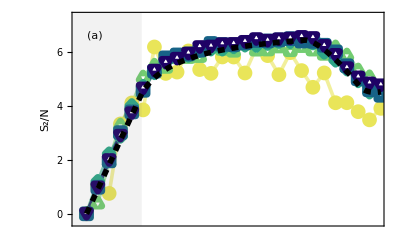

```mathematica
(* Plot the time evolution of the Renyi-2 entanglement entropy for various system sizes against the QFT prediction. *)
Fig10a=Show[ListLinePlot[Renyi2EntanglementEntropySimulatorDataOBC,PlotRange->{{-0.15,5.15},{-0.3,7.3}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->Fig4PlotStyles,FrameLabel->{None,Style["S_2/N",Black,FontSize->15]},
FrameTicks->{{{0,2,4,6,8},None},{None,{{2*τOBC[25,5,1,2],"2τ/N"}}}},
FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],ListPlot[Renyi2EntanglementEntropySimulatorDataOBC,PlotMarkers->Fig4PlotMarkers],
Graphics[{Black,FontSize->15,Style[Text["(a)",{0.15,6.6}],Bold],Gray,Opacity[0.1],Rectangle[{-1,-1},{2*τOBC[25,5,1,2],9}]}],Plot[Renyi2EntanglementEntropyQFTCurveOBC[t],{t,0,5.2},PlotStyle->{{Black,Thickness[0.01],Dashed}},PlotRange->All], 
(* ImageSize->{Automatic,180.4}] *)
ImageSize->{Automatic,196.4}]
```

##### Longer time evolution

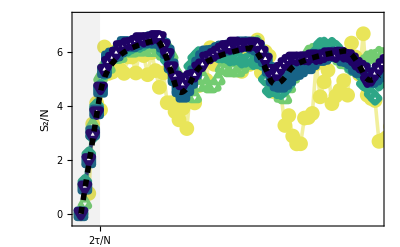

```mathematica
(* Plot the time evolution of the Renyi-2 entanglement entropy for various system sizes against the QFT prediction. *)
Fig10aLongerEvolution=Show[ListLinePlot[Renyi2EntanglementEntropySimulatorDataOBC,PlotRange->{{-0.15,15.15},{-0.3,7.3}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->Fig4PlotStyles,FrameLabel->{None,Style["S_2/N",Black,FontSize->15]},
FrameTicks->{{{0,2,4,6,8},None},{{{2*τOBC[25,5,1,2],"2τ/N"}},None}},
FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],ListPlot[Renyi2EntanglementEntropySimulatorDataOBC,PlotMarkers->Fig4PlotMarkers],
Graphics[{Gray,Opacity[0.1],Rectangle[{-1,-1},{2*τOBC[25,5,1,2],8}]}],
(* Graphics[{Black,FontSize->15,Style[Text["(a)",{0.1,7.6}],Bold],Gray,Opacity[0.15],Rectangle[{τOBC[25,5,1,2],-1},{2*τOBC[25,5,1,2],9}]}], *)Plot[Renyi2EntanglementEntropyQFTCurveOBC[t],{t,0,15.2},PlotStyle->{{Black,Thickness[0.01],Dashed}},PlotRange->All],
ImageSize->{Automatic,250}]
```

#### (b) Renyi-2 mutual information

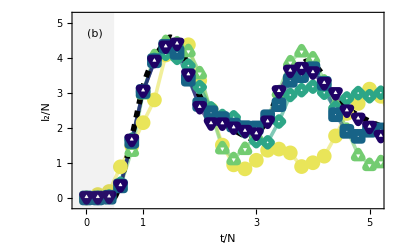

```mathematica
(* Plot the time evolution of the Renyi-2 mutual information for various system sizes against the QFT prediction. *)
Fig10b=Show[ListLinePlot[Renyi2MutualInformationSimulatorDataOBC,PlotRange->{{-0.15,5.15},{-0.2,5.2}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->Fig4PlotStyles,FrameLabel->{Style["t/N",Black,FontSize->15],Style["I_2/N",Black,FontSize->15]},FrameTicks->{{{0,1,2,3,4,5},None},{{0,{τOBC[25,5,1,2],"τ/N"},1,2,3,4,5},None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],
Plot[Renyi2MutualInformationQFTCurveOBC[t],{t,0,5.2},PlotStyle->{{Black,Thickness[0.01],Dashed}},PlotRange->All],
ListPlot[Renyi2MutualInformationSimulatorDataOBC,PlotMarkers->Fig4PlotMarkers],Graphics[{Black,FontSize->15,Style[Text["(b)",{0.15,4.7}],Bold],Gray,Opacity[0.1],Rectangle[{-1,-1},{τOBC[25,5,1,2],9}]}],
ImageSize->{Automatic,219.4}]
```

### Final figure

```mathematica
(* Combine the latter two plots with a bar legend. *)
Fig10=Rasterize[Legended[Grid[{{Rasterize[Fig10a,ImageResolution->300,ImageSize->{Automatic,196.4}],,,,,,,,,,,,},
{Rasterize[Fig10b,ImageResolution->300,ImageSize->{Automatic,219.4}]}},Alignment->Left,Spacings->{0,0.2}],Placed[Rasterize[BarLegend[{ContinuousColors[0.8,0],{0,0.8}},LabelStyle->{Black,FontSize->12},LegendMarkerSize->160,Ticks->{{0,"5"},{0.2,"10"},{0.4,"15"},{0.6,"20"},{0.8,"25"}},LegendLabel->Style["N",FontSize->14,Black]],ImageResolution->300],{1,0.56}]],
ImageResolution->300]
```

-Graphics-

```mathematica
(* To export the pdf. *)
(* Export[FileNameJoin[{"EntanglementGenerationOBC.pdf"}],Fig10,ImageResolution->Automatic,"AllowRasterization"->True] *)
```

EntanglementGenerationOBC.pdf

```mathematica
(* Compute τ/N. *)
τOBC[25,5,1,2]//N
```

0.487859